## Introduction

Make pics for paper

## Main sim

$Aborted

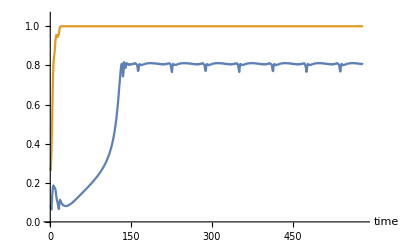

```mathematica
(*Preamble*)
{dt,n,T}={0.5,50,3000}; 
{J,k}={1,1};
{e,b}={0.85,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]

ListPlot[{Abs[Wp],Abs[Wm]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05}]
```

```mathematica
{x,theta}=znew;
{ξ,η}={x+theta,x-theta};
{sp,ϕp}={Abs[Wp][[-1]],Arg[Wp][[-1]]};
{sm,ϕm}={Abs[Wm][[-1]],Arg[Wm][[-1]]};
α=pin[[1]];
```

```mathematica
Chop[esnew]//TableForm
```

-3.31858 | -3.29294 | -3.26593 | -3.23758 | -3.20789 | -3.17686 | -3.14451 | -3.11085 | -3.07589 | -3.03965 | -3.00213 | -2.96336 | -2.92335 | -2.88211 | -2.83966 | -2.79601 | -2.7512 | -2.70522 | -2.65811 | -2.60988 | -2.56056 | -2.51016 | -2.4587 | -2.40622 | -2.35272 | -2.29824 | -2.24279 | -2.18641 | -2.12911 | -2.07092 | -2.01187 | -1.95198 | -1.89128 | -1.8298 | -1.76756 | -1.70459 | -1.64093 | -1.57659 | -1.5116 | -1.446 | -1.37982 | -1.31308 | -1.24582 | -1.17807 | -1.10985 | -1.0412 | -0.97215 | -0.902733 | -0.832978 | -0.76292 | -0.69259 | -0.622022 | -0.551248 | -0.480302 | -0.409217 | -0.338027 | -0.266766 | -0.195469 | -0.12417 | -0.052903 | 0.0182957 | 0.0893912 | 0.160348 | 0.23113 | 0.301701 | 0.372024 | 0.442062 | 0.511778 | 0.581134 | 0.650092 | 0.718611 | 0.786652 | 0.854176 | 0.921139 | 0.987499 | 1.05321 | 1.11823 | 1.18252 | 1.24601 | 1.30867 | 1.37043 | 1.43124 | -3.54591 | -3.54393 | -3.5407 | -3.53617 | -3.53034 | -3.52319 | -3.5147 | -3.50485 | -3.49365 | -3.48108 | -3.46714 | -3.45181 | -3.43511 | -3.41703 | -3.39756 | -3.37671 | -3.35449 | -3.33089 | -3.30593 | -3.2796 | -3.25193 | -3.2229 | -3.19254 | -3.16085 | -3.12784 | -3.09353 | -3.05793 | -3.02105 | -2.9829 | -2.94351 | -2.90288 | -2.86103 | -2.81798 | -2.77375 | -2.72835 | -2.68181 | -2.63414 | -2.58536 | -2.53549 | -2.48456 | -2.43259 | -2.37959 | -2.3256 | -2.27063 | -2.21472 | -2.15787 | -2.10013 | -2.0415 | -1.98203 | -1.92173 | -1.86064 | -1.79877 | -1.73617 | -1.67285 | -1.60884 | -1.54417 | -1.47888 | -1.41298 | -1.34652 | -1.27952 | -1.212 | -1.14401 | -1.07558 | -1.00672 | -0.937486 | -0.867895 | -0.797985 | -0.727787 | -0.657334 | -0.586659 | -0.515794 | -0.444774 | -0.373633 | -0.302403 | -0.23112 | -0.159817 | -0.08853 | -0.017293 | 0.0538585 | 0.124889 | 0.195763 | 0.266444 | 0.336895 | 0.407081 | 0.476963 | 0.546504 | 0.615665 | 0.684408 | 0.752694 | 0.820481 | 0.88773 | 0.954397 | 1.02044 | 1.08581 | 1.15047 | 1.21437 | 1.27745 | 1.33967 | 1.40096 | 1.46128 | -3.54507 | -3.54247 | -3.5386 | -3.53342 | -3.52693 | -3.51911 | -3.50994 | -3.49942 | -3.48754 | -3.47428 | -3.45965 | -3.44363 | -3.42624 | -3.40746 | -3.38731 | -3.36577 | -3.34286 | -3.31858
2.75784×10^-8 | 2.75415×10^-8 | 2.7506×10^-8 | 2.74719×10^-8 | 2.74391×10^-8 | 2.74077×10^-8 | 2.73777×10^-8 | 2.73489×10^-8 | 2.73214×10^-8 | 2.72952×10^-8 | 2.72702×10^-8 | 2.72464×10^-8 | 2.72239×10^-8 | 2.72025×10^-8 | 2.71824×10^-8 | 2.71634×10^-8 | 2.71456×10^-8 | 2.71289×10^-8 | 2.71133×10^-8 | 2.70989×10^-8 | 2.70856×10^-8 | 2.70734×10^-8 | 2.70623×10^-8 | 2.70523×10^-8 | 2.70434×10^-8 | 2.70356×10^-8 | 2.70289×10^-8 | 2.70232×10^-8 | 2.70186×10^-8 | 2.70151×10^-8 | 2.70126×10^-8 | 2.70112×10^-8 | 2.70109×10^-8 | 2.70116×10^-8 | 2.70134×10^-8 | 2.70162×10^-8 | 2.70201×10^-8 | 2.70251×10^-8 | 2.70312×10^-8 | 2.70383×10^-8 | 2.70465×10^-8 | 2.70558×10^-8 | 2.70662×10^-8 | 2.70777×10^-8 | 2.70903×10^-8 | 2.7104×10^-8 | 2.71188×10^-8 | 2.71347×10^-8 | 2.71518×10^-8 | 2.71701×10^-8 | 2.71895×10^-8 | 2.72101×10^-8 | 2.72318×10^-8 | 2.72548×10^-8 | 2.7279×10^-8 | 2.73044×10^-8 | 2.73311×10^-8 | 2.73591×10^-8 | 2.73883×10^-8 | 2.74188×10^-8 | 2.74507×10^-8 | 2.7484×10^-8 | 2.75186×10^-8 | 2.75546×10^-8 | 2.7592×10^-8 | 2.76309×10^-8 | 2.76713×10^-8 | 2.77132×10^-8 | 2.77567×10^-8 | 2.78017×10^-8 | 2.78484×10^-8 | 2.78967×10^-8 | 2.79468×10^-8 | 2.79985×10^-8 | 2.80521×10^-8 | 2.81075×10^-8 | 2.81649×10^-8 | 2.82241×10^-8 | 2.82855×10^-8 | 2.83489×10^-8 | 2.84144×10^-8 | 2.84822×10^-8 | 2.8492×10^-8 | 2.84239×10^-8 | 2.8358×10^-8 | 2.82943×10^-8 | 2.82327×10^-8 | 2.81731×10^-8 | 2.81155×10^-8 | 2.80598×10^-8 | 2.8006×10^-8 | 2.7954×10^-8 | 2.79037×10^-8 | 2.78551×10^-8 | 2.78082×10^-8 | 2.7763×10^-8 | 2.77193×10^-8 | 2.76771×10^-8 | 2.76365×10^-8 | 2.75974×10^-8 | 2.75598×10^-8 | 2.75236×10^-8 | 2.74888×10^-8 | 2.74553×10^-8 | 2.74233×10^-8 | 2.73925×10^-8 | 2.73631×10^-8 | 2.7335×10^-8 | 2.73081×10^-8 | 2.72825×10^-8 | 2.72581×10^-8 | 2.7235×10^-8 | 2.72131×10^-8 | 2.71923×10^-8 | 2.71727×10^-8 | 2.71543×10^-8 | 2.71371×10^-8 | 2.7121×10^-8 | 2.7106×10^-8 | 2.70921×10^-8 | 2.70794×10^-8 | 2.70677×10^-8 | 2.70572×10^-8 | 2.70478×10^-8 | 2.70394×10^-8 | 2.70321×10^-8 | 2.70259×10^-8 | 2.70208×10^-8 | 2.70167×10^-8 | 2.70137×10^-8 | 2.70118×10^-8 | 2.70109×10^-8 | 2.70111×10^-8 | 2.70123×10^-8 | 2.70147×10^-8 | 2.7018×10^-8 | 2.70225×10^-8 | 2.7028×10^-8 | 2.70346×10^-8 | 2.70423×10^-8 | 2.7051×10^-8 | 2.70609×10^-8 | 2.70718×10^-8 | 2.70838×10^-8 | 2.7097×10^-8 | 2.71112×10^-8 | 2.71266×10^-8 | 2.71431×10^-8 | 2.71608×10^-8 | 2.71796×10^-8 | 2.71996×10^-8 | 2.72208×10^-8 | 2.72432×10^-8 | 2.72667×10^-8 | 2.72916×10^-8 | 2.73176×10^-8 | 2.73449×10^-8 | 2.73735×10^-8 | 2.74034×10^-8 | 2.74346×10^-8 | 2.74672×10^-8 | 2.75011×10^-8 | 2.75364×10^-8 | 2.75731×10^-8 | 2.76113×10^-8 | 2.76509×10^-8 | 2.76921×10^-8 | 2.77348×10^-8 | 2.7779×10^-8 | 2.78249×10^-8 | 2.78723×10^-8 | 2.79215×10^-8 | 2.79724×10^-8 | 2.80251×10^-8 | 2.80796×10^-8 | 2.8136×10^-8 | 2.81943×10^-8 | 2.82545×10^-8 | 2.83169×10^-8 | 2.83814×10^-8 | 2.8448×10^-8 | 2.8517×10^-8 | 2.84576×10^-8 | 2.83906×10^-8 | 2.83259×10^-8 | 2.82632×10^-8 | 2.82026×10^-8 | 2.81441×10^-8 | 2.80874×10^-8 | 2.80327×10^-8 | 2.79798×10^-8 | 2.79286×10^-8 | 2.78792×10^-8 | 2.78315×10^-8 | 2.77854×10^-8 | 2.77409×10^-8 | 2.7698×10^-8 | 2.76567×10^-8 | 2.76168×10^-8 | 2.75784×10^-8

```mathematica
-2 Cos[η/2]Sin[ξ/2-α]+k sp Sin[ϕp-ξ]
```

{-3.31858,-3.29294,-3.26593,-3.23758,-3.20789,-3.17686,-3.14451,-3.11085,-3.07589,-3.03965,-3.00213,-2.96336,-2.92335,-2.88211,-2.83966,-2.79601,-2.7512,-2.70522,-2.65811,-2.60988,-2.56056,-2.51016,-2.4587,-2.40622,-2.35272,-2.29824,-2.24279,-2.18641,-2.12911,-2.07092,-2.01187,-1.95198,-1.89128,-1.8298,-1.76756,-1.70459,-1.64093,-1.57659,-1.5116,-1.446,-1.37982,-1.31308,-1.24582,-1.17807,-1.10985,-1.0412,-0.97215,-0.902733,-0.832978,-0.76292,-0.69259,-0.622022,-0.551248,-0.480302,-0.409217,-0.338027,-0.266766,-0.195469,-0.12417,-0.052903,0.0182957,0.0893912,0.160348,0.23113,0.301701,0.372024,0.442062,0.511778,0.581134,0.650092,0.718611,0.786652,0.854176,0.921139,0.987499,1.05321,1.11823,1.18252,1.24601,1.30867,1.37043,1.43124,-3.54591,-3.54393,-3.5407,-3.53617,-3.53034,-3.52319,-3.5147,-3.50485,-3.49365,-3.48108,-3.46714,-3.45181,-3.43511,-3.41703,-3.39756,-3.37671,-3.35449,-3.33089,-3.30593,-3.2796,-3.25193,-3.2229,-3.19254,-3.16085,-3.12784,-3.09353,-3.05793,-3.02105,-2.9829,-2.94351,-2.90288,-2.86103,-2.81798,-2.77375,-2.72835,-2.68181,-2.63414,-2.58536,-2.53549,-2.48456,-2.43259,-2.37959,-2.3256,-2.27063,-2.21472,-2.15787,-2.10013,-2.0415,-1.98203,-1.92173,-1.86064,-1.79877,-1.73617,-1.67285,-1.60884,-1.54417,-1.47888,-1.41298,-1.34652,-1.27952,-1.212,-1.14401,-1.07558,-1.00672,-0.937486,-0.867895,-0.797985,-0.727787,-0.657334,-0.586659,-0.515794,-0.444774,-0.373633,-0.302403,-0.23112,-0.159817,-0.08853,-0.017293,0.0538585,0.124889,0.195763,0.266444,0.336895,0.407081,0.476963,0.546504,0.615665,0.684408,0.752694,0.820481,0.88773,0.954397,1.02044,1.08581,1.15047,1.21437,1.27745,1.33967,1.40096,1.46128,-3.54507,-3.54247,-3.5386,-3.53342,-3.52693,-3.51911,-3.50994,-3.49942,-3.48754,-3.47428,-3.45965,-3.44363,-3.42624,-3.40746,-3.38731,-3.36577,-3.34286,-3.31858}

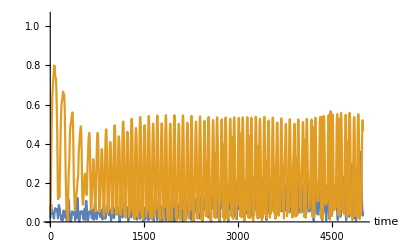

```mathematica
(*Preamble*)
{dt,n,T}={0.1,100,500}; 
{J,k}={-0.1,-0.1};
{e,b}={1.1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
]

ListPlot[{Abs[Wp],Abs[Wm]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

## Bistability

### Old

```mathematica
(*Preamble*)
data1=Table[
{dt,n,T}={0.5,200,200}; 
{J}={1};
{e,b}={0.8,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{k,Sp,Sm},
{k,k1,k2,dk}
];

(*Preamble*)
data2=Table[
{dt,n,T}={0.5,200,100}; 
{J}={1};
{e,b}={0.8,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{k,Sp,Sm},
{k,k1,k2,dk}
];
```

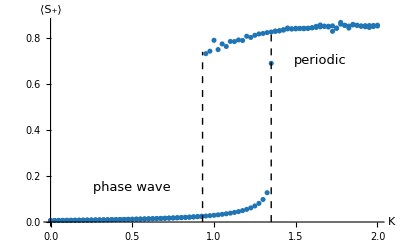

```mathematica
{pa,pb}={0.93,1.35};
p1=ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["K",18,Italic],Style["⟨S_+⟩",18,Italic]},LabelStyle->15,PlotStyle->{ColorData[99,"ColorList"]},
Epilog->{
Dashed,Line[{{pa,0},{pa,0.74}}],Line[{{pb,0},{pb,0.82}}],
Text[Style["phase wave",13],{0.5,0.15}],
Text[Style["periodic",13],{1.65,0.7}]
}]
SetDirectory[NotebookDirectory[]];
Export["figures/hysteresis.png",p1];
```

### New S(K)

```mathematica
{k1,k2,dk}={0.5,1.4,0.01};

(*Preamble*)
data1=Table[
{dt,n,T}={0.5,300,200}; 
{J}={k};
{e,b}={0.8,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{k,Sp,Sm},
{k,k1,k2,dk}
];

(*Preamble*)
data2=Table[
{dt,n,T}={0.5,200,100}; 
{J}={1};
{e,b}={0.8,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{k,Sp,Sm},
{k,k1,k2,dk}
];
```

#### Save data

```mathematica
data1={{0.5,0.0057007306736598165,1.},{0.51,0.005782874160178795,1.},{0.52,0.005867419660034285,1.},{0.53,0.005954474106911049,1.},{0.54,0.00604415087855718,1.},{0.55,0.006136570289711538,1.},{0.56,0.006231860131035073,1.},{0.5700000000000001,0.006330156259092654,1.},{0.58,0.006431603243089891,1.},{0.59,0.0065363550748956945,1.},{0.6,0.006644575949692663,1.},{0.61,0.006756441125536943,1.},{0.62,0.006872137871372762,1.},{0.63,0.006991866514246258,1.},{0.64,0.007115841598088976,1.},{0.65,0.0072442931682254,1.},{0.66,0.007377468197708266,1.},{0.67,0.0075156321742578976,1.},{0.6799999999999999,0.007659070869197043,1.},{0.69,0.0078080923132725875,1.},{0.7,0.007963029008221122,1.},{0.71,0.008124240407481857,1.},{0.72,0.008292115705165696,1.},{0.73,0.008467076978989763,1.},{0.74,0.008649582740679567,1.},{0.75,0.008840131956946396,1.},{0.76,0.009039268615544736,1.},{0.77,0.009247586924680069,1.},{0.78,0.009465737250874299,1.},{0.79,0.009694432920677057,1.},{0.8,0.009934458036864708,1.},{0.81,0.010186676490279671,1.},{0.8200000000000001,0.010452042386813213,1.},{0.8300000000000001,0.010731612156104114,1.},{0.8400000000000001,0.011026558667877162,1.},{0.8500000000000001,0.011338187756232304,1.},{0.86,0.01166795764613861,1.},{0.87,0.012017501896484989,1.},{0.88,0.01238865662762377,1.},{0.89,0.012783492999699218,1.},{0.9,0.013204356166886986,1.},{0.91,0.013653912272088247,1.},{0.9199999999999999,0.014135205494604342,1.},{0.9299999999999999,0.014651727758325399,1.},{0.94,0.015207504555672364,1.},{0.95,0.015807201352866087,1.},{0.96,0.016456256787275192,1.},{0.97,0.017161050507760126,1.},{0.98,0.01792911774018813,1.},{0.99,0.01876942455101128,1.},{1.,0.019692729636498717,1.},{1.01,0.02071205457180432,1.},{1.02,0.021843329210973803,1.},{1.03,0.023106269472489536,1.},{1.04,0.024525466313563442,1.},{1.05,0.02613250431389805,1.},{1.06,0.027967724414555414,1.},{1.07,0.03008499118788548,1.},{1.08,0.032555789596497416,1.},{1.0899999999999999,0.035482555712702174,1.},{1.1,0.0390068041433333,1.},{1.1099999999999999,0.0433495807138759,1.},{1.12,0.04880331705466809,1.},{1.13,0.056009264012879326,1.},{1.1400000000000001,0.06623259662011094,1.},{1.15,0.0822489026115021,1.},{1.1600000000000001,0.7557800433028059,1.},{1.17,0.8272903135386092,1.},{1.1800000000000002,0.830724171684383,1.},{1.19,0.8322762960195877,1.},{1.2000000000000002,0.833428584994928,1.},{1.21,0.8345213256981479,1.},{1.22,0.836284511782687,0.9999999487516199},{1.23,0.8370060382011497,1.},{1.24,0.8383591826806254,0.9999670745436413},{1.25,0.8393272203608532,1.},{1.26,0.8410106430738377,0.9999999999999941},{1.27,0.8421859905569461,0.9999999999817789},{1.28,0.8432781024635805,0.999999999996476},{1.29,0.8442634842942811,0.9999999999837433},{1.3,0.8446297798167048,0.999999999933484},{1.31,0.8313585965919176,0.8522212375423259},{1.32,0.8464230264629343,0.9999999853545257},{1.33,0.8477570178723886,0.9999999999999722},{1.3399999999999999,0.8353149566328112,0.8658371753797633},{1.35,0.8492878085163296,0.9999955759841025},{1.3599999999999999,0.8416217413779156,0.8704950443540419},{1.37,0.8417809430524751,0.8657804408339902},{1.38,0.8509805219265135,0.9999985715040594},{1.3900000000000001,0.8467898022234432,0.8702376825496336},{1.4,0.8522626135244319,0.9997661275716508}};
```

```mathematica
data2={{0.5,0.0120050882489539,0.999998770439927},{0.51,0.012174730485044674,0.999998794462483},{0.52,0.012347937061774783,0.9999988187443914},{0.53,0.012524821652542198,0.9999988432860583},{0.54,0.012705502754003442,0.9999988680875824},{0.55,0.012890104255311806,0.9999988931486531},{0.56,0.013078755200328918,0.9999989184686249},{0.5700000000000001,0.013271590946594752,0.9999989440462994},{0.58,0.013468751858502962,0.999998969880199},{0.59,0.013670386056557843,0.9999989959680458},{0.6,0.013876647958383873,0.9999990223070689},{0.61,0.014087698778458557,0.9999990488938996},{0.62,0.014303706962818807,0.9999990757244843},{0.63,0.014524850871690555,0.999999102793672},{0.64,0.014751317650047174,0.9999991300954141},{0.65,0.014983294820939463,0.9999991576238494},{0.66,0.015220997198874623,0.9999991853696231},{0.67,0.01546463439476547,0.9999992133242612},{0.6799999999999999,0.015714432370538406,0.9999992414772004},{0.69,0.01597062622663194,0.9999992698166584},{0.7,0.016233483701059117,0.9999992983271387},{0.71,0.016503227154582068,0.999999326997213},{0.72,0.016780169204335227,0.9999993558058171},{0.73,0.017064591876005515,0.9999993847342055},{0.74,0.017356849724652346,0.9999994137565977},{0.75,0.01765717877912497,0.9999994428551214},{0.76,0.017965966923876964,0.9999994719981383},{0.77,0.018283523011120333,0.9999995011575901},{0.78,0.018610424760995836,0.9999995302865727},{0.79,0.01894692872732649,0.9999995593554813},{0.8,0.01929340156613592,0.9999995883231579},{0.81,0.019650647827137734,0.9999996171242717},{0.8200000000000001,0.0200183610645995,0.9999996457382184},{0.8300000000000001,0.02039788740936235,0.9999996740678023},{0.8400000000000001,0.020789964444768355,0.9999997020418101},{0.8500000000000001,0.02119459803574172,0.9999997296049088},{0.86,0.021611851948682807,0.9999997566838003},{0.87,0.022043326045234218,0.999999783155715},{0.88,0.022490391320017577,0.999999808903494},{0.89,0.022954187262990484,0.9999998338085283},{0.9,0.02343588967886982,0.9999998577407978},{0.91,0.023936231212507167,0.9999998805611865},{0.9199999999999999,0.02444732059917431,0.9999999021841939},{0.9299999999999999,0.02498921689757642,0.9999999222447022},{0.94,0.025580506520478215,0.99999994050146},{0.95,0.02625369536468225,0.9999999567256753},{0.96,0.7325622765964263,0.871245204085517},{0.97,0.7624337262343365,0.8877498958544614},{0.98,0.7810006212260124,0.9417525569234956},{0.99,0.7866266224522833,0.9849644642404863},{1.,0.7894396299174398,0.999999818252122},{1.01,0.7896710141225155,0.9822845436841534},{1.02,0.754312256001423,0.8637234119907485},{1.03,0.7850882130808243,0.9422423777328042},{1.04,0.7501191586596374,0.8644625297048026},{1.05,0.7731038123802502,0.9294812760444053},{1.06,0.782813780145211,0.920071781299541},{1.07,0.7671927815643128,0.8540042794695635},{1.08,0.7675336759604738,0.8771126398107993},{1.0899999999999999,0.7830261212250798,0.9132071591813274},{1.1,0.7811222360658954,0.8911838327645272},{1.1099999999999999,0.7833251403257057,0.8598038531699876},{1.12,0.7848272085751621,0.846120046691724},{1.13,0.7770316803628878,0.8419522372352182},{1.1400000000000001,0.785561219368667,0.8674435841674454},{1.15,0.7909250222770936,0.8924839253117766},{1.1600000000000001,0.7924306001782313,0.8791384084374458},{1.17,0.7869027285345629,0.8499062183979055},{1.1800000000000002,0.7901213308693865,0.8388505322381915},{1.19,0.8002402210201003,0.8283388663273938},{1.2000000000000002,0.8074933392371232,0.8227982293876233},{1.21,0.8085250232452963,0.8173929822118302},{1.22,0.8041642687812349,0.8152777861375944},{1.23,0.8053261064571005,0.8169397560291427},{1.24,0.8086426786511298,0.8286840284316233},{1.25,0.8114474347812591,0.8350072465365534},{1.26,0.8110852064279124,0.8445382198009451},{1.27,0.8120671423735087,0.8564340107419648},{1.28,0.8169337656509489,0.8577346629712965},{1.29,0.819390519739095,0.8606218060044646},{1.3,0.8202911332974216,0.87128675899989},{1.31,0.8213480582650251,0.8624058300393204},{1.32,0.8225994468029617,0.8612074777137422},{1.33,0.8223737599473081,0.8629694168239449},{1.3399999999999999,0.8239294460343656,0.861287613918605},{1.35,0.825933129826548,0.8676878915638891},{1.3599999999999999,0.8276158567201555,0.8717728826072776},{1.37,0.8289220065215532,0.8732670757439569},{1.38,0.8309761465548624,0.8722527138104887},{1.3900000000000001,0.83288136841515,0.8566853585243327},{1.4,0.8354625817426724,0.8392866066056538}};
```

#### Plot data

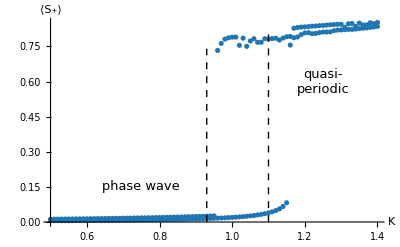

```mathematica
{pa,pb}={0.93,1.1};
p1=ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["K",18,Italic],Style["⟨S_+⟩",18,Italic]},LabelStyle->15,PlotStyle->{ColorData[99,"ColorList"]},PlotRange->{{0.5,1.4},Automatic},
Epilog->{
Dashed,Line[{{pa,0},{pa,0.74}}],Line[{{pb,0},{pb,0.82}}],
Text[Style["phase wave",13],{0.75,0.15}],
Text[Style["quasi-\nperiodic",13],{1.25,0.6}]
}]
SetDirectory[NotebookDirectory[]];
Export["figures/hysteresis.png",p1];
```

### New S(E)

```mathematica
{e1,e2,de}={0.7,0.9,0.005};

(*Preamble*)
data1=Table[
{dt,n,T}={0.5,300,200}; 
{K,k}={1,1};
{b}={1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{e,Sp,Sm},
{e,e1,e2,de}
];

(*Preamble*)
data2=Table[
{dt,n,T}={0.5,300,200}; 
{K,k}={1,1};
{b}={1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
cutoff=Round[0.9 *Length[Wp]];
{Sp,Sm}={Abs[Wp][[cutoff;;-1]]//Mean,Abs[Wm][[cutoff;;-1]]//Mean};
{e,Sp,Sm},
{e,e1,e2,de}
];
```

#### Save data

```mathematica
data1={{0.5,0.0057007306736598165,1.},{0.51,0.005782874160178795,1.},{0.52,0.005867419660034285,1.},{0.53,0.005954474106911049,1.},{0.54,0.00604415087855718,1.},{0.55,0.006136570289711538,1.},{0.56,0.006231860131035073,1.},{0.5700000000000001,0.006330156259092654,1.},{0.58,0.006431603243089891,1.},{0.59,0.0065363550748956945,1.},{0.6,0.006644575949692663,1.},{0.61,0.006756441125536943,1.},{0.62,0.006872137871372762,1.},{0.63,0.006991866514246258,1.},{0.64,0.007115841598088976,1.},{0.65,0.0072442931682254,1.},{0.66,0.007377468197708266,1.},{0.67,0.0075156321742578976,1.},{0.6799999999999999,0.007659070869197043,1.},{0.69,0.0078080923132725875,1.},{0.7,0.007963029008221122,1.},{0.71,0.008124240407481857,1.},{0.72,0.008292115705165696,1.},{0.73,0.008467076978989763,1.},{0.74,0.008649582740679567,1.},{0.75,0.008840131956946396,1.},{0.76,0.009039268615544736,1.},{0.77,0.009247586924680069,1.},{0.78,0.009465737250874299,1.},{0.79,0.009694432920677057,1.},{0.8,0.009934458036864708,1.},{0.81,0.010186676490279671,1.},{0.8200000000000001,0.010452042386813213,1.},{0.8300000000000001,0.010731612156104114,1.},{0.8400000000000001,0.011026558667877162,1.},{0.8500000000000001,0.011338187756232304,1.},{0.86,0.01166795764613861,1.},{0.87,0.012017501896484989,1.},{0.88,0.01238865662762377,1.},{0.89,0.012783492999699218,1.},{0.9,0.013204356166886986,1.},{0.91,0.013653912272088247,1.},{0.9199999999999999,0.014135205494604342,1.},{0.9299999999999999,0.014651727758325399,1.},{0.94,0.015207504555672364,1.},{0.95,0.015807201352866087,1.},{0.96,0.016456256787275192,1.},{0.97,0.017161050507760126,1.},{0.98,0.01792911774018813,1.},{0.99,0.01876942455101128,1.},{1.,0.019692729636498717,1.},{1.01,0.02071205457180432,1.},{1.02,0.021843329210973803,1.},{1.03,0.023106269472489536,1.},{1.04,0.024525466313563442,1.},{1.05,0.02613250431389805,1.},{1.06,0.027967724414555414,1.},{1.07,0.03008499118788548,1.},{1.08,0.032555789596497416,1.},{1.0899999999999999,0.035482555712702174,1.},{1.1,0.0390068041433333,1.},{1.1099999999999999,0.0433495807138759,1.},{1.12,0.04880331705466809,1.},{1.13,0.056009264012879326,1.},{1.1400000000000001,0.06623259662011094,1.},{1.15,0.0822489026115021,1.},{1.1600000000000001,0.7557800433028059,1.},{1.17,0.8272903135386092,1.},{1.1800000000000002,0.830724171684383,1.},{1.19,0.8322762960195877,1.},{1.2000000000000002,0.833428584994928,1.},{1.21,0.8345213256981479,1.},{1.22,0.836284511782687,0.9999999487516199},{1.23,0.8370060382011497,1.},{1.24,0.8383591826806254,0.9999670745436413},{1.25,0.8393272203608532,1.},{1.26,0.8410106430738377,0.9999999999999941},{1.27,0.8421859905569461,0.9999999999817789},{1.28,0.8432781024635805,0.999999999996476},{1.29,0.8442634842942811,0.9999999999837433},{1.3,0.8446297798167048,0.999999999933484},{1.31,0.8313585965919176,0.8522212375423259},{1.32,0.8464230264629343,0.9999999853545257},{1.33,0.8477570178723886,0.9999999999999722},{1.3399999999999999,0.8353149566328112,0.8658371753797633},{1.35,0.8492878085163296,0.9999955759841025},{1.3599999999999999,0.8416217413779156,0.8704950443540419},{1.37,0.8417809430524751,0.8657804408339902},{1.38,0.8509805219265135,0.9999985715040594},{1.3900000000000001,0.8467898022234432,0.8702376825496336},{1.4,0.8522626135244319,0.9997661275716508}};
```

```mathematica
data2={{0.5,0.0120050882489539,0.999998770439927},{0.51,0.012174730485044674,0.999998794462483},{0.52,0.012347937061774783,0.9999988187443914},{0.53,0.012524821652542198,0.9999988432860583},{0.54,0.012705502754003442,0.9999988680875824},{0.55,0.012890104255311806,0.9999988931486531},{0.56,0.013078755200328918,0.9999989184686249},{0.5700000000000001,0.013271590946594752,0.9999989440462994},{0.58,0.013468751858502962,0.999998969880199},{0.59,0.013670386056557843,0.9999989959680458},{0.6,0.013876647958383873,0.9999990223070689},{0.61,0.014087698778458557,0.9999990488938996},{0.62,0.014303706962818807,0.9999990757244843},{0.63,0.014524850871690555,0.999999102793672},{0.64,0.014751317650047174,0.9999991300954141},{0.65,0.014983294820939463,0.9999991576238494},{0.66,0.015220997198874623,0.9999991853696231},{0.67,0.01546463439476547,0.9999992133242612},{0.6799999999999999,0.015714432370538406,0.9999992414772004},{0.69,0.01597062622663194,0.9999992698166584},{0.7,0.016233483701059117,0.9999992983271387},{0.71,0.016503227154582068,0.999999326997213},{0.72,0.016780169204335227,0.9999993558058171},{0.73,0.017064591876005515,0.9999993847342055},{0.74,0.017356849724652346,0.9999994137565977},{0.75,0.01765717877912497,0.9999994428551214},{0.76,0.017965966923876964,0.9999994719981383},{0.77,0.018283523011120333,0.9999995011575901},{0.78,0.018610424760995836,0.9999995302865727},{0.79,0.01894692872732649,0.9999995593554813},{0.8,0.01929340156613592,0.9999995883231579},{0.81,0.019650647827137734,0.9999996171242717},{0.8200000000000001,0.0200183610645995,0.9999996457382184},{0.8300000000000001,0.02039788740936235,0.9999996740678023},{0.8400000000000001,0.020789964444768355,0.9999997020418101},{0.8500000000000001,0.02119459803574172,0.9999997296049088},{0.86,0.021611851948682807,0.9999997566838003},{0.87,0.022043326045234218,0.999999783155715},{0.88,0.022490391320017577,0.999999808903494},{0.89,0.022954187262990484,0.9999998338085283},{0.9,0.02343588967886982,0.9999998577407978},{0.91,0.023936231212507167,0.9999998805611865},{0.9199999999999999,0.02444732059917431,0.9999999021841939},{0.9299999999999999,0.02498921689757642,0.9999999222447022},{0.94,0.025580506520478215,0.99999994050146},{0.95,0.02625369536468225,0.9999999567256753},{0.96,0.7325622765964263,0.871245204085517},{0.97,0.7624337262343365,0.8877498958544614},{0.98,0.7810006212260124,0.9417525569234956},{0.99,0.7866266224522833,0.9849644642404863},{1.,0.7894396299174398,0.999999818252122},{1.01,0.7896710141225155,0.9822845436841534},{1.02,0.754312256001423,0.8637234119907485},{1.03,0.7850882130808243,0.9422423777328042},{1.04,0.7501191586596374,0.8644625297048026},{1.05,0.7731038123802502,0.9294812760444053},{1.06,0.782813780145211,0.920071781299541},{1.07,0.7671927815643128,0.8540042794695635},{1.08,0.7675336759604738,0.8771126398107993},{1.0899999999999999,0.7830261212250798,0.9132071591813274},{1.1,0.7811222360658954,0.8911838327645272},{1.1099999999999999,0.7833251403257057,0.8598038531699876},{1.12,0.7848272085751621,0.846120046691724},{1.13,0.7770316803628878,0.8419522372352182},{1.1400000000000001,0.785561219368667,0.8674435841674454},{1.15,0.7909250222770936,0.8924839253117766},{1.1600000000000001,0.7924306001782313,0.8791384084374458},{1.17,0.7869027285345629,0.8499062183979055},{1.1800000000000002,0.7901213308693865,0.8388505322381915},{1.19,0.8002402210201003,0.8283388663273938},{1.2000000000000002,0.8074933392371232,0.8227982293876233},{1.21,0.8085250232452963,0.8173929822118302},{1.22,0.8041642687812349,0.8152777861375944},{1.23,0.8053261064571005,0.8169397560291427},{1.24,0.8086426786511298,0.8286840284316233},{1.25,0.8114474347812591,0.8350072465365534},{1.26,0.8110852064279124,0.8445382198009451},{1.27,0.8120671423735087,0.8564340107419648},{1.28,0.8169337656509489,0.8577346629712965},{1.29,0.819390519739095,0.8606218060044646},{1.3,0.8202911332974216,0.87128675899989},{1.31,0.8213480582650251,0.8624058300393204},{1.32,0.8225994468029617,0.8612074777137422},{1.33,0.8223737599473081,0.8629694168239449},{1.3399999999999999,0.8239294460343656,0.861287613918605},{1.35,0.825933129826548,0.8676878915638891},{1.3599999999999999,0.8276158567201555,0.8717728826072776},{1.37,0.8289220065215532,0.8732670757439569},{1.38,0.8309761465548624,0.8722527138104887},{1.3900000000000001,0.83288136841515,0.8566853585243327},{1.4,0.8354625817426724,0.8392866066056538}};
```

#### Plot data

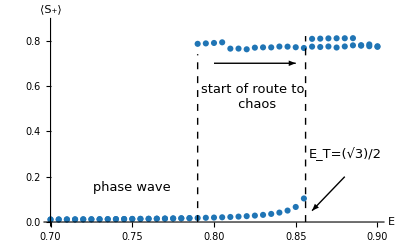

```mathematica
{pa,pb}={0.79,√3/2-0.01};
p1=ListPlot[{data1[[All,{1,2}]],data2[[All,{1,2}]]},AxesLabel->{Style["E",18,Italic],Style["⟨S_+⟩",18,Italic]},LabelStyle->15,PlotStyle->{ColorData[99,"ColorList"]},PlotRange->{{0.7,0.9},{0,0.88}},
Epilog->{
Arrow[{{0.8,0.7},{0.85,0.7}}],
Arrow[{{0.88,0.2},{0.86,0.05}}],
Dashed,Line[{{pa,0},{pa,0.74}}],Line[{{pb,0},{pb,0.82}}],
Text[Style["phase wave",13],{0.75,0.15}],
Text[Style["start of route to \n chaos",13],{0.825,0.55}],
Text[Style["E_T=(√3)/2",13],{0.88,0.3}]
}]
SetDirectory[NotebookDirectory[]];
Export["figures/hysteresisE.png",p1];
```

## Split phase wave

### Main

```mathematica
(*Preamble*)
{dt,n,T}={0.1,200,500}; 
{J,k}={-50,-50};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
```

$Aborted

```mathematica
run2[k1_,n_,T_]:=Block[{dt,J,e,b,b1,b2,Ex,Eθ,z0,pin,znew,z00,Wp,Wp1,Wm1,Wm,t,NT,temp,xi,eta,x,θ,k,theta},

(*Preamble*)
{dt}={0.1}; 
{J,k}={k1,k1};
{e,b}={0,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];

(*Stuff here*)
{x,θ}=znew;
temp={Mod[x+θ,2π]-π,Mod[x-θ,2π]-π}ᵀ;
temp=Sort[temp];
{xi,eta}={temp[[All,1]],temp[[All,2]]};
Return[{Mod[x,2π]-π,Mod[θ,2π]-π,xi,eta,Abs[Wp][[-1]],Abs[Wm][[-1]]}]
]
```

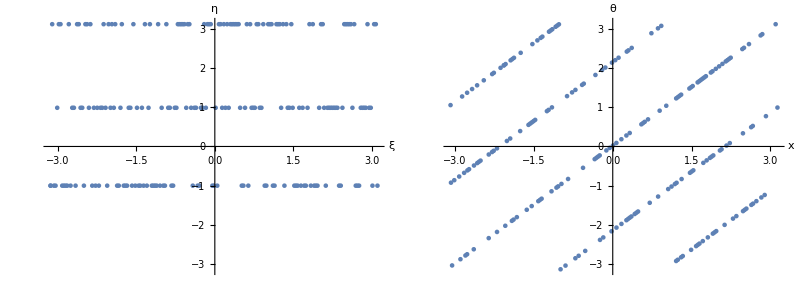

{{0.,76},{4.1,35},{2.,43},{2.1,45}}

{0.38,4.1,0.000190268,0.0278524}

```mathematica
n=200;
{x,theta,xi,eta,Sp,Sm}=run2[-50,n,1000];
p1=ListPlot[{xi,eta}ᵀ,PlotRange->{-π,π},AxesLabel->{"ξ","η"},LabelStyle->15,ImageSize->Medium];
p2=ListPlot[{x,theta}ᵀ,PlotRange->{-π,π},AxesLabel->{"x","θ"},LabelStyle->15,ImageSize->Medium];
Grid[{{p1,p2}}]
Tally[Mod[Round[Abs[Differences[eta]],0.1],6.3]]
temp=Tally[Mod[Round[Abs[Differences[eta]],0.1],6.3]];
delta=Max[temp[[All,1]]];
p=N[Max[temp[[All,2]]]/n];
{p,delta,Sp,Sm}
```

#### Iterate

```mathematica
n=50;
realdata=ParallelTable[
{x,theta,xi,eta,Sp,Sm}=run2[k,n,500];
temp=Tally[Mod[Round[Abs[Differences[eta]],0.1],6.3]];
delta=Max[temp[[All,1]]];
p=N[Max[temp[[All,2]]]/n];
{k,p,delta,Sm},
{k,0,-10,-0.1}
];
```

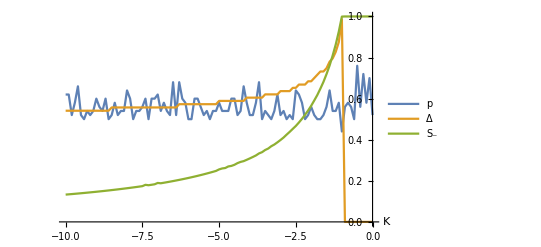

```mathematica
ListPlot[{realdata[[All,{1,2}]],{realdata[[All,1]],realdata[[All,3]]/(2π)}ᵀ,realdata[[All,{1,4}]]},Joined->True,PlotRange->All,AxesLabel->{"K"},PlotLegends->{"p","Δ","S_-"}]
```

### Find state

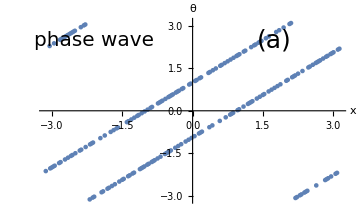

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={-2,-2};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p1=ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["phase wave",20],{-2.1,2.5}],Text[Style["(a)",25],{1.75,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

```mathematica
Dimensions[x]
```

{200}

```mathematica
temp={Mod[x+θ,2π]-π,Mod[x-θ,2π]-π}ᵀ;
temp=Sort[temp];
{xi,eta}={temp[[All,1]],temp[[All,2]]};
```

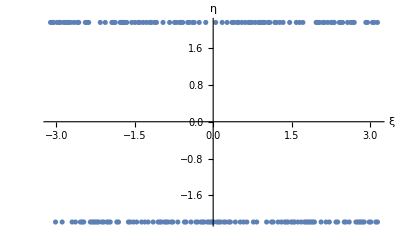

```mathematica
ListPlot[{xi,eta}ᵀ,AxesLabel->{"ξ","η"}]
```

### S(K)

#### Make data

```mathematica
dataReal=ParallelTable[
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.1,200,100}; 
{J,k}={K,K};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5 Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
(*If[Sp≤Sm,{Sp,Sm}={Sm,Sp}];*)
{K,Sp,Sm},
{K,-5,5,0.1}
];
```

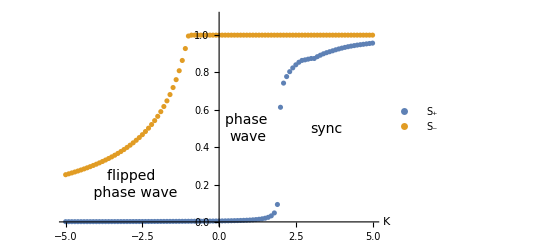

figures/order-pars-undriven.png

```mathematica
p1b=ListPlot[{dataReal[[All,{1,2}]],dataReal[[All,{1,3}]]},AxesLabel->{Style["K",22,Italic]},PlotLegends->{Style["S_+",19],Style["S_-",19]},LabelStyle->16,PlotRange->{0,1.1},Epilog->{Dashed,(*Line[{{-1,0},{-1,1}}],Line[{{2,0},{2,1}}],*)Text[Style["sync",14],{3.5,0.5}],Text[Style["phase \nwave",14],{0.95,0.5}],Text[Style["flipped \n phase wave",14],{-2.8,0.2}]}]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-undriven.png",p1b]
```

#### Gourab’s Ansatz

{0,0.540302}

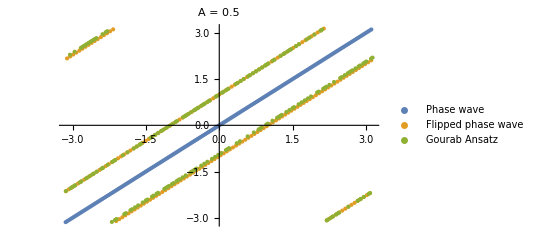

```mathematica
{A,n}={0.5,200};
α=Table[(2π i)/n,{i,0,n-1}];
data=Table[{α[[i]]+(-1)^i A,α[[i]]+(-1)^(i-1)A}//mod,{i,1,n}];
{x,θ}={data[[All,1]],data[[All,2]]};
{sp1,sm1}={N[Total[Exp[ⅈ(x+θ)]]/Length[x]],N[Total[Exp[ⅈ(x-θ)]]/Length[x]]}//Chop
{xreal,θreal}=znew;
ListPlot[{{α,α}ᵀ//mod,data,{xreal,θreal}ᵀ//mod},PlotLegends->{"Phase wave","Flipped phase wave","Gourab Ansatz"},PlotLabel->"A = 0.5",LabelStyle->15]
```

Perfect!

#### Solve self consistency equations

```mathematica
Sin[xreal-θreal]
```

{-0.84245,0.806711,0.806711,0.806712,0.806712,0.806712,-0.842451,-0.842451,-0.842452,0.806714,-0.842452,0.806715,0.806715,-0.842454,-0.842454,0.806717,-0.842455,0.806718,0.806719,-0.842456,-0.842456,-0.842456,-0.842457,0.80672,0.80672,-0.842457,-0.842457,0.80672,0.80672,-0.842456,0.806719,-0.842456,0.806718,-0.842455,-0.842455,0.806717,-0.842454,0.806716,0.806715,-0.842453,-0.842452,0.806714,0.806713,-0.842451,0.806712,0.806712,-0.84245,-0.84245,-0.84245,0.806711,0.806711,0.806711,0.806711,-0.84245,0.806712,0.806712,-0.842451,0.806713,0.806713,0.806714,-0.842453,0.806715,-0.842453,0.806716,-0.842454,-0.842455,0.806718,0.806718,0.806719,0.806719,0.806719,-0.842456,-0.842457,0.80672,-0.842457,0.80672,-0.842457,0.80672,-0.842457,-0.842456,0.806719,-0.842456,0.806718,-0.842455,0.806717,-0.842454,0.806716,-0.842454,-0.842453,0.806715,0.806714,0.806714,-0.842452,-0.842451,-0.842451,-0.842451,0.806712,-0.84245,0.806711,-0.84245,-0.84245,-0.84245,-0.84245,0.806712,-0.842451,-0.842451,-0.842451,0.806713,-0.842452,-0.842452,0.806715,0.806715,0.806716,-0.842454,-0.842454,0.806717,0.806718,-0.842455,-0.842456,0.806719,-0.842456,-0.842457,0.80672,0.80672,0.80672,0.80672,-0.842457,-0.842457,0.80672,-0.842456,0.806719,-0.842456,0.806718,0.806718,-0.842455,-0.842454,0.806716,-0.842453,0.806715,-0.842453,0.806714,-0.842452,0.806713,-0.842451,0.806712,-0.842451,-0.84245,-0.84245,0.806711,0.806711,-0.84245,-0.84245,0.806712,0.806712,0.806712,-0.842451,0.806713,-0.842452,-0.842452,0.806714,-0.842453,-0.842453,-0.842454,0.806716,0.806717,-0.842455,0.806718,-0.842456,0.806719,0.806719,0.806719,0.80672,-0.842457,0.80672,-0.842457,0.80672,0.80672,-0.842457,0.80672,0.806719,0.806719,-0.842456,-0.842455,0.806718,0.806717,-0.842454,-0.842454,0.806715,-0.842453,-0.842452,0.806714,-0.842452,-0.842451,-0.842451,0.806712,0.806712,0.806712,0.806711,0.806711,0.806711}

```mathematica
eqn=Cos[2 a]+b1(Sin[a]/Sin[2a]);
TrigExpand[Together[eqn]]
```

Cos[a]^2+Sec[a]/2-Sin[a]^2

```mathematica
Solve[Cos[2 a]==-2/j1 Sin[a]/Sin[2a]/.j1->-2,a]//N
```

{{a→ConditionalExpression[-0.485062+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[0.485062+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(-2.00497-0.319561 ⅈ)+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(2.00497+0.319561 ⅈ)+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(-2.00497+0.319561 ⅈ)+6.28319 C[1], C[1]∈ℤ]},{a→ConditionalExpression[(2.00497-0.319561 ⅈ)+6.28319 C[1], C[1]∈ℤ]}}

```mathematica
Solve[Cos[2 a]==B Sin[a]/Sin[2a],a]
```

{{a→ConditionalExpression[ArcTan[1/2 (-2/(3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))-((-9 B+√3 √(-8+27 B^2))^(1/3))/3^(2/3)),-1/6 √(24-(12 3^(1/3))/((-9 B+√3 √(-8+27 B^2))^(2/3))-3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[1/2 (-2/(3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))-((-9 B+√3 √(-8+27 B^2))^(1/3))/3^(2/3)),1/6 √(24-(12 3^(1/3))/((-9 B+√3 √(-8+27 B^2))^(2/3))-3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(1+ⅈ √3)/(2 3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))+((1-ⅈ √3) (-9 B+√3 √(-8+27 B^2))^(1/3))/(4 3^(2/3)),-√(2/3-1/(4 3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))-ⅈ/(2 3^(1/6) (-9 B+√3 √(-8+27 B^2))^(2/3))+3^(1/3)/(4 (-9 B+√3 √(-8+27 B^2))^(2/3))+(ⅈ (-9 B+√3 √(-8+27 B^2))^(2/3))/(8 3^(5/6))+((-9 B+√3 √(-8+27 B^2))^(2/3))/(24 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(1+ⅈ √3)/(2 3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))+((1-ⅈ √3) (-9 B+√3 √(-8+27 B^2))^(1/3))/(4 3^(2/3)),√(2/3-1/(4 3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))-ⅈ/(2 3^(1/6) (-9 B+√3 √(-8+27 B^2))^(2/3))+3^(1/3)/(4 (-9 B+√3 √(-8+27 B^2))^(2/3))+(ⅈ (-9 B+√3 √(-8+27 B^2))^(2/3))/(8 3^(5/6))+((-9 B+√3 √(-8+27 B^2))^(2/3))/(24 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(1-ⅈ √3)/(2 3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))+((1+ⅈ √3) (-9 B+√3 √(-8+27 B^2))^(1/3))/(4 3^(2/3)),-√(2/3-1/(4 3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))+ⅈ/(2 3^(1/6) (-9 B+√3 √(-8+27 B^2))^(2/3))+3^(1/3)/(4 (-9 B+√3 √(-8+27 B^2))^(2/3))-(ⅈ (-9 B+√3 √(-8+27 B^2))^(2/3))/(8 3^(5/6))+((-9 B+√3 √(-8+27 B^2))^(2/3))/(24 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(1-ⅈ √3)/(2 3^(1/3) (-9 B+√3 √(-8+27 B^2))^(1/3))+((1+ⅈ √3) (-9 B+√3 √(-8+27 B^2))^(1/3))/(4 3^(2/3)),√(2/3-1/(4 3^(2/3) (-9 B+√3 √(-8+27 B^2))^(2/3))+ⅈ/(2 3^(1/6) (-9 B+√3 √(-8+27 B^2))^(2/3))+3^(1/3)/(4 (-9 B+√3 √(-8+27 B^2))^(2/3))-(ⅈ (-9 B+√3 √(-8+27 B^2))^(2/3))/(8 3^(5/6))+((-9 B+√3 √(-8+27 B^2))^(2/3))/(24 3^(1/3)))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Cos[2*0.48506171125871744]
```

0.565198

```mathematica
asol
```

{a→0.+ArcTan[(0.550321 k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))+(0.302853 (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,-0.166667 √(24.-(10.9027 k^2)/((-9. k^2+1.73205 √(-1. k^4 (-27.+2. k^2)))^(2/3))-(3.30193 (-9. k^2+1.73205 √(-1. k^4 (-27.+2. k^2)))^(2/3))/k^2)],a→0.+ArcTan[(0.550321 k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))+(0.302853 (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,0.166667 √(24.-(10.9027 k^2)/((-9. k^2+1.73205 √(-1. k^4 (-27.+2. k^2)))^(2/3))-(3.30193 (-9. k^2+1.73205 √(-1. k^4 (-27.+2. k^2)))^(2/3))/k^2)],a→0.+ArcTan[-((0.275161+0.476592 ⅈ) k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))-((0.151427-0.262279 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,-1. √(0.666667+((0.151427-0.262279 ⅈ) k^2)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))+((0.0458601+0.079432 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))/k^2)],a→0.+ArcTan[-((0.275161+0.476592 ⅈ) k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))-((0.151427-0.262279 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,√(0.666667+((0.151427-0.262279 ⅈ) k^2)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))+((0.0458601+0.079432 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))/k^2)],a→0.+ArcTan[-((0.275161-0.476592 ⅈ) k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))-((0.151427+0.262279 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,-1. √(0.666667+((0.151427+0.262279 ⅈ) k^2)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))+((0.0458601-0.079432 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))/k^2)],a→0.+ArcTan[-((0.275161-0.476592 ⅈ) k)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))-((0.151427+0.262279 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(1/3))/k,√(0.666667+((0.151427+0.262279 ⅈ) k^2)/((-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))+((0.0458601-0.079432 ⅈ) (-9. k^2+1.73205 √(27. k^4-2. k^6))^(2/3))/k^2)]}

```mathematica
eqn=Cos[2 a]+2/k Sin[a]/Sin[2a]
```

```mathematica
TrigExpand[Sin[4a]]
```

4 Cos[a]^3 Sin[a]-4 Cos[a] Sin[a]^3

```mathematica
TrigExpand[Cos[a]^3]
```

Cos[a]^3

```mathematica
ContourPlot[]
```

```mathematica
Solve[Sin[4a]+b3 Sin[a]==0,a]
```

{{a→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(2/3)^(1/3)/((-9 b3+√3 √(-32+27 b3^2))^(1/3))+((-9 b3+√3 √(-32+27 b3^2))^(1/3))/(2 2^(1/3) 3^(2/3)),-(√(48-(24 2^(2/3) 3^(1/3))/((-9 b3+√3 √(-32+27 b3^2))^(2/3))-2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3)))/(6 √2)]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[(2/3)^(1/3)/((-9 b3+√3 √(-32+27 b3^2))^(1/3))+((-9 b3+√3 √(-32+27 b3^2))^(1/3))/(2 2^(1/3) 3^(2/3)),(√(48-(24 2^(2/3) 3^(1/3))/((-9 b3+√3 √(-32+27 b3^2))^(2/3))-2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3)))/(6 √2)]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[-(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))-((1-ⅈ √3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))/(4 2^(1/3) 3^(2/3)),-√(2/3+(3/2)^(1/3)/(2 (-9 b3+√3 √(-32+27 b3^2))^(2/3))-1/(2 2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3))-ⅈ/(2^(1/3) 3^(1/6) (-9 b3+√3 √(-32+27 b3^2))^(2/3))+(ⅈ (-9 b3+√3 √(-32+27 b3^2))^(2/3))/(8 2^(2/3) 3^(5/6))+((-9 b3+√3 √(-32+27 b3^2))^(2/3))/(24 2^(2/3) 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[-(1+ⅈ √3)/(2^(2/3) 3^(1/3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))-((1-ⅈ √3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))/(4 2^(1/3) 3^(2/3)),√(2/3+(3/2)^(1/3)/(2 (-9 b3+√3 √(-32+27 b3^2))^(2/3))-1/(2 2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3))-ⅈ/(2^(1/3) 3^(1/6) (-9 b3+√3 √(-32+27 b3^2))^(2/3))+(ⅈ (-9 b3+√3 √(-32+27 b3^2))^(2/3))/(8 2^(2/3) 3^(5/6))+((-9 b3+√3 √(-32+27 b3^2))^(2/3))/(24 2^(2/3) 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[-(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))-((1+ⅈ √3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))/(4 2^(1/3) 3^(2/3)),-√(2/3+(3/2)^(1/3)/(2 (-9 b3+√3 √(-32+27 b3^2))^(2/3))-1/(2 2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3))+ⅈ/(2^(1/3) 3^(1/6) (-9 b3+√3 √(-32+27 b3^2))^(2/3))-(ⅈ (-9 b3+√3 √(-32+27 b3^2))^(2/3))/(8 2^(2/3) 3^(5/6))+((-9 b3+√3 √(-32+27 b3^2))^(2/3))/(24 2^(2/3) 3^(1/3)))]+2 π C[1], C[1]∈ℤ]},{a→ConditionalExpression[ArcTan[-(1-ⅈ √3)/(2^(2/3) 3^(1/3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))-((1+ⅈ √3) (-9 b3+√3 √(-32+27 b3^2))^(1/3))/(4 2^(1/3) 3^(2/3)),√(2/3+(3/2)^(1/3)/(2 (-9 b3+√3 √(-32+27 b3^2))^(2/3))-1/(2 2^(1/3) 3^(2/3) (-9 b3+√3 √(-32+27 b3^2))^(2/3))+ⅈ/(2^(1/3) 3^(1/6) (-9 b3+√3 √(-32+27 b3^2))^(2/3))-(ⅈ (-9 b3+√3 √(-32+27 b3^2))^(2/3))/(8 2^(2/3) 3^(5/6))+((-9 b3+√3 √(-32+27 b3^2))^(2/3))/(24 2^(2/3) 3^(1/3)))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Clear[k];
asol=Flatten[Solve[Cos[2 a]==-2/k Sin[a]/Sin[2a],a]]/.C[1]->0//Flatten;
asol/.k->-2//TableForm
```

a→-π-ArcTan[(√(24-(-3 (36-4 √57))^(2/3)/(2 2^(1/3))+(24 (-6)^(1/3))/(36-4 √57)^(2/3)))/(6 ((-2)^(2/3)/(3 (36-4 √57))^(1/3)-(-36+4 √57)^(1/3)/(2 6^(2/3))))]
a→π+ArcTan[(√(24-(-3 (36-4 √57))^(2/3)/(2 2^(1/3))+(24 (-6)^(1/3))/(36-4 √57)^(2/3)))/(6 ((-2)^(2/3)/(3 (36-4 √57))^(1/3)-(-36+4 √57)^(1/3)/(2 6^(2/3))))]
a→-ArcTan[(√(2/3+((-1)^(5/6) 2^(1/3))/(3^(1/6) (36-4 √57)^(2/3))-(-3)^(1/3)/(2 (36-4 √57))^(2/3)+(-1)^(1/3)/(6 (36-4 √57))^(2/3)+(ⅈ (-36+4 √57)^(2/3))/(16 2^(1/3) 3^(5/6))+(-36+4 √57)^(2/3)/(48 6^(1/3))))/(-((-1)^(2/3) (1+ⅈ √3))/(6 (36-4 √57))^(1/3)+((1-ⅈ √3) (-36+4 √57)^(1/3))/(4 6^(2/3)))]
a→ArcTan[(√(2/3+((-1)^(5/6) 2^(1/3))/(3^(1/6) (36-4 √57)^(2/3))-(-3)^(1/3)/(2 (36-4 √57))^(2/3)+(-1)^(1/3)/(6 (36-4 √57))^(2/3)+(ⅈ (-36+4 √57)^(2/3))/(16 2^(1/3) 3^(5/6))+(-36+4 √57)^(2/3)/(48 6^(1/3))))/(-((-1)^(2/3) (1+ⅈ √3))/(6 (36-4 √57))^(1/3)+((1-ⅈ √3) (-36+4 √57)^(1/3))/(4 6^(2/3)))]
a→-π-ArcTan[(√(2/3-((-1)^(5/6) 2^(1/3))/(3^(1/6) (36-4 √57)^(2/3))-(-3)^(1/3)/(2 (36-4 √57))^(2/3)+(-1)^(1/3)/(6 (36-4 √57))^(2/3)-(ⅈ (-36+4 √57)^(2/3))/(16 2^(1/3) 3^(5/6))+(-36+4 √57)^(2/3)/(48 6^(1/3))))/(-((-1)^(2/3) (1-ⅈ √3))/(6 (36-4 √57))^(1/3)+((1+ⅈ √3) (-36+4 √57)^(1/3))/(4 6^(2/3)))]
a→π+ArcTan[(√(2/3-((-1)^(5/6) 2^(1/3))/(3^(1/6) (36-4 √57)^(2/3))-(-3)^(1/3)/(2 (36-4 √57))^(2/3)+(-1)^(1/3)/(6 (36-4 √57))^(2/3)-(ⅈ (-36+4 √57)^(2/3))/(16 2^(1/3) 3^(5/6))+(-36+4 √57)^(2/3)/(48 6^(1/3))))/(-((-1)^(2/3) (1-ⅈ √3))/(6 (36-4 √57))^(1/3)+((1+ⅈ √3) (-36+4 √57)^(1/3))/(4 6^(2/3)))]

```mathematica
smsol=Simplify[(Cos[a]^2-Sin[a]^2)/.asol[[3]]/.C[1]->0//TrigExpand]
```

(2 ⅈ 6^(1/3) (ⅈ+√3) k^4+2^(2/3) 3^(1/6) (-1-ⅈ √3) √(27 k^4-2 k^6) (-9 k^2+√(81 k^4-6 k^6))^(1/3)+k^2 (-9 k^2+√(81 k^4-6 k^6))^(1/3) (9 ⅈ 2^(2/3) 3^(1/6)+3 6^(2/3)-4 (-9 k^2+√(81 k^4-6 k^6))^(1/3)))/(12 k^2 (-9 k^2+√(81 k^4-6 k^6))^(2/3))

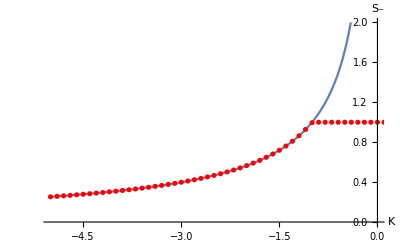

```mathematica
p1=Plot[1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)/.k->k1,{k1,-5,0},AxesLabel->{"K","S_-"},LabelStyle->15,PlotRange->{0,2}];
p2=ListPlot[dataReal[[All,{1,3}]],PlotStyle->{Red}];
Show[{p1,p2}]
```

```mathematica
TrigExpand[Cos[2a]]
```

Cos[a]^2-Sin[a]^2

```mathematica
Clear[s,k];
ssol=Solve[k^2 s^3+k^2 s^2-2==0,s]//TableForm
```

s→1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)
s→-1/3-((1+ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1-ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)
s→-1/3-((1-ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1+ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)

```mathematica
1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)//TeXForm
```

\frac{1}{3} \left(\frac{k^2}{\sqrt[3]{-k^6+27 k^4+3 \sqrt{3} \sqrt{27 k^8-2 k^{10}}}}+\frac{\sqrt[3]{-k^6+27 k^4+3 \sqrt{3} \sqrt{27 k^8-2 k^{10}}}}{k^2}-1\right)

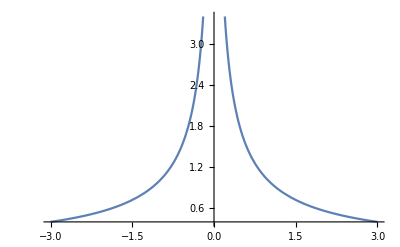

```mathematica
Plot[s/.ssol/.k->k1,{k1,-3,3}]
```

#### My ansatz

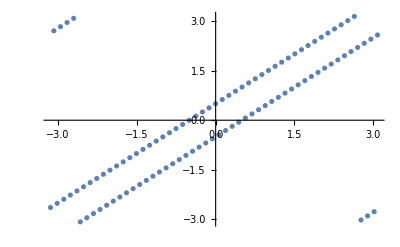

{0,0.877583}

```mathematica
mod[x_]:=Mod[x,2π]-π;
{A,n}={0.5,100};
α=Table[(2π i)/n,{i,0,n-1}];
data=Table[{α[[i]],α[[i]]+(-1)^(i-1)A}//mod,{i,1,n}];
ListPlot[data]
{x,θ}={data[[All,1]],data[[All,2]]};
{sp1,sm1}={N[Total[Exp[ⅈ(x+θ)]]/Length[x]],N[Total[Exp[ⅈ(x-θ)]]/Length[x]]}//Chop
```

### Solve cubic myself

```mathematica
temp1=k^2 s^3+k^2 s^2-2+2 e^2;
ssol=Solve[temp1==0,s];
Manipulate[Plot[s/.ssol[[1]]/.e->e1,{k,-10,10},PlotRange->{0,1},AxesLabel->{"K","S_-"},LabelStyle->15],{e1,0,2}]
```

```mathematica
ssol[[1]]/.{k->K,e->Ε}
```

{s→-1/3+(2^(1/3) K^2)/(3 (54 K^4-2 K^6-54 K^4 Ε^2+√(-4 K^12+(54 K^4-2 K^6-54 K^4 Ε^2)^2))^(1/3))+((54 K^4-2 K^6-54 K^4 Ε^2+√(-4 K^12+(54 K^4-2 K^6-54 K^4 Ε^2)^2))^(1/3))/(3 2^(1/3) K^2)}

```mathematica
TeXForm[-1/3+(2^(1/3) K^2)/(3 (54 K^4-2 K^6-54 K^4 Ε^2+√(-4 K^12+(54 K^4-2 K^6-54 K^4 Ε^2)^2))^(1/3))+((54 K^4-2 K^6-54 K^4 Ε^2+√(-4 K^12+(54 K^4-2 K^6-54 K^4 Ε^2)^2))^(1/3))/(3 2^(1/3) K^2)]
```

\frac{\sqrt[3]{2} K^2}{3 \sqrt[3]{-54 E^2 K^4+\sqrt{\left(-54 E^2 K^4-2 K^6+54 K^4\right)^2-4 K^{12}}-2 K^6+54 K^4}}+\frac{\sqrt[3]{-54 E^2 K^4+\sqrt{\left(-54 E^2 K^4-2 K^6+54 K^4\right)^2-4 K^{12}}-2
   K^6+54 K^4}}{3 \sqrt[3]{2} K^2}-\frac{1}{3}

```mathematica
FullSimplify[ssol[[1]]]
```

{s→-1/3+(k^4+(-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(2/3))/(3 k^2 (-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(1/3))}

```mathematica
TeXForm[(-1+e^2) k^8 (-27+27 e^2+2 k^2)]/.k->K
```

\left(e^2-1\right) K^8 \left(27 e^2+2 K^2-27\right)

```mathematica
Manipulate[Plot[-1/3+(k^4+(-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(2/3))/(3 k^2 (-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(1/3))/.k->k1,{e,0,2}],{k1,-10,0}]
```

```mathematica
Solve[-1/3+(k^4+(-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(2/3))/(3 k^2 (-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(1/3))==1,e]
```

{{e→-√(1-k^2)},{e→√(1-k^2)}}

```mathematica
Solve[-1/3+(k^4+(-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(2/3))/(3 k^2 (-27 (-1+e^2) k^4-k^6+3 √3 √((-1+e^2) k^8 (-27+27 e^2+2 k^2)))^(1/3))==0,e]
```

{{e→-1},{e→1}}

## Bursty async

### Make data

#### (k, E) = (-0.1, 1.1)

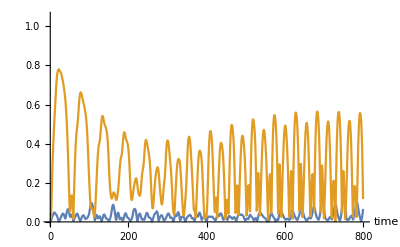

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={-0.1,-0.1};
{e,b}={1.1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wpa,Wma}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wpa,Abs[Wp1]];AppendTo[Wma,Abs[Wm1]];
]

ListPlot[{Abs[Wpa],Abs[Wma]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

#### (k, E) = (-0.1, 1.1)

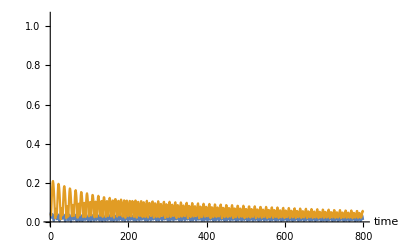

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={-0.1,-0.1};
{e,b}={2,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wpb,Wmb}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wpb,Abs[Wp1]];AppendTo[Wmb,Abs[Wm1]];
]

ListPlot[{Abs[Wpb],Abs[Wmb]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

#### (k, E) = (-1.5, 1.1)

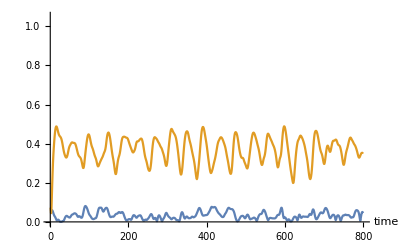

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={-1.5,-1.5};
{e,b}={0.85,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wp3,Wm3}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp3,Abs[Wp1]];AppendTo[Wm3,Abs[Wm1]];
]

ListPlot[{Abs[Wp3],Abs[Wm3]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

#### E = 3

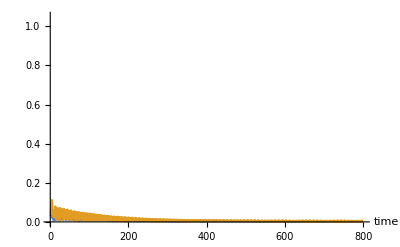

```mathematica
(*Preamble*)
{dt,n,T}={0.25,300,200}; 
{J,k}={-1.5,-1.5};
{e,b}={3,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*Main sim*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wp4,Wm4}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp4,Abs[Wp1]];AppendTo[Wm4,Abs[Wm1]];
]

ListPlot[{Abs[Wp4],Abs[Wm4]},Joined->True,AxesLabel->{"time"},LabelStyle->15,PlotRange->{0,1.05},PlotRange->All]
```

### Make plot

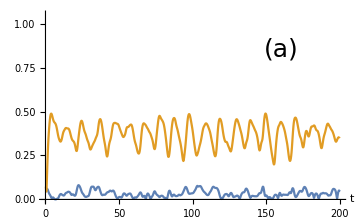
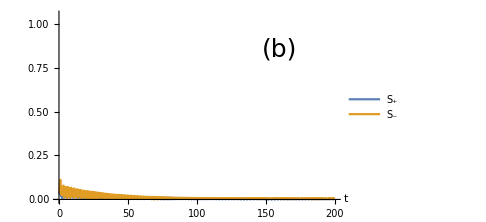
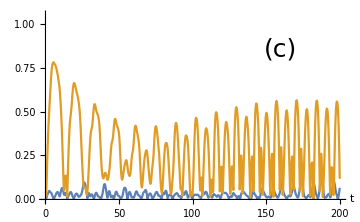
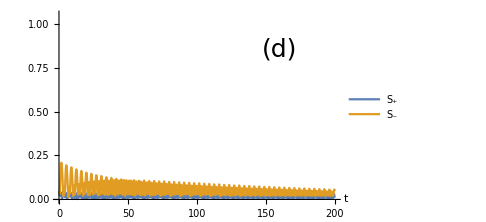
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
ts=Table[dt*i,{i,1,Length[Wp3]}];
p1=ListPlot[{{ts,Abs[Wp3]}ᵀ,{ts,Abs[Wm3]}ᵀ},Joined->True,AxesLabel->{Style["t",30,Italic]},LabelStyle->20,PlotRange->{0,1.05},PlotRange->All,ImageSize->Medium,Epilog->{Text[Style["(a)",25],{160,0.85}]}];
p2=ListPlot[{{ts,Abs[Wp4]}ᵀ,{ts,Abs[Wm4]}ᵀ},Joined->True,AxesLabel->{Style["t",30,Italic]},LabelStyle->20,PlotRange->{0,1.05},PlotRange->All,ImageSize->Medium,PlotLegends->{Style["S_+",30],Style["S_-",30]},
Epilog->{Text[Style["(b)",25],{160,0.85}]}];
ts=Table[dt*i,{i,1,Length[Wpa]}];
p3=ListPlot[{{ts,Abs[Wpa]}ᵀ,{ts,Abs[Wma]}ᵀ},Joined->True,AxesLabel->{Style["t",30,Italic]},LabelStyle->20,PlotRange->{0,1.05},PlotRange->All,ImageSize->Medium,
Epilog->{Text[Style["(c)",25],{160,0.85}]}];
p4=ListPlot[{{ts,Abs[Wpb]}ᵀ,{ts,Abs[Wmb]}ᵀ},Joined->True,AxesLabel->{Style["t",30,Italic]},LabelStyle->20,PlotRange->{0,1.05},PlotRange->All,ImageSize->Medium,PlotLegends->{Style["S_+",30],Style["S_-",30]},
Epilog->{Text[Style["(d)",25],{160,0.85}]}];
ptog=Grid[{{p1,p2},{p3,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/busty-async.png",ptog];
```

## Bif diagram (K,E) space

### Develop

```mathematica
findVmean[xs_,thetas_,dt_]:=Module[{vx,vtheta,tcutoff,vxMean,vthetaMean,vMean,n,T,index},
{vx,vtheta}={{},{}};
{T,n}=Dimensions[xs];
tcutoff=Round[0.9T];
vxMean=Table[Mean[Differences[xs[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vthetaMean=Table[Mean[Differences[thetas[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vMean=√(vxMean^2+vthetaMean^2);
Return[vMean]
];

run[k1_,e_]:=Module[{J,K,dt,n,T,k,b,Ex,Eθ,b1,b2,t,NT,pin,z00,z0,znew,Wp,Wm,Wp1,Wm1,xs,x,theta,thetas,vmean,Sp,Sm,cutoff},

{dt,n,T}={0.5,100,100}; 
{J,k,b}={k1,k1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
{xs,thetas}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp1,Wm1}=findWs[znew];
{x,theta}=znew;AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
AppendTo[xs,x];AppendTo[thetas,theta];
];

cutoff=Round[0.9Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
vmean=findVmean[xs,thetas];
Return[{vmean,Sp,Sm}]
]
```

### Make data

```mathematica
data=Flatten[ParallelTable[{k,e,run[k,e]},{k,-5,5,0.05},{e,0,1.5,0.05}],1];
data={data[[All,1]],data[[All,2]],data[[All,3]]/Max[data[[All,3]]]}ᵀ;
```

$Aborted

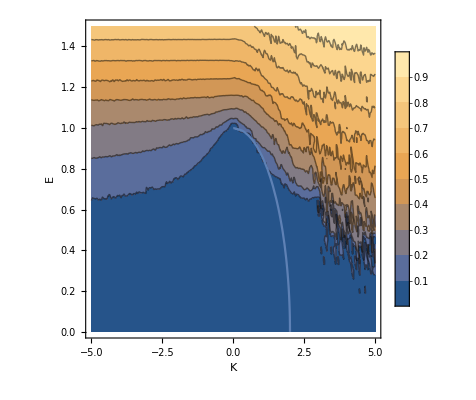

```mathematica
p1=ListContourPlot[data//Chop,FrameLabel->{Style["K",17,Italic],Style["E",Italic,17]},PlotLegends->Automatic,LabelStyle->13];
p2=ContourPlot[√(1-e1^2)-k/2==0,{k,-5,5},{e1,0,2}];
Show[{p1,p2}]
```

### Data here

```mathematica
{dt,n,T}={0.5,100,100}; 
{J,k,b}={k1,k1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
{xs,thetas}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp1,Wm1}=findWs[znew];
{x,theta}=znew;AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
AppendTo[xs,x];AppendTo[thetas,theta];
];

cutoff=Round[0.9Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
vmean=findVmean[xs,thetas];
```

```mathematica
data=Flatten[ParallelTable[{k,e,run[k,e]}//Flatten,{k,-3,3,1},{e,0,1.2,0.5}],1];
```

```mathematica
data=Flatten[ParallelTable[{k,e,run[k,e]}//Flatten,{k,-3,3,0.025},{e,0,1.2,0.025}],1];
(*data=Flatten[ParallelTable[{k,e,run[k,e]}//Flatten,{k,-3,3,1},{e,0,1.2,0.5}],1];*)
data={data[[All,1]],data[[All,2]],data[[All,3]]/Max[data[[All,3]]],data[[All,4]],data[[All,5]]}ᵀ;
```

$Aborted

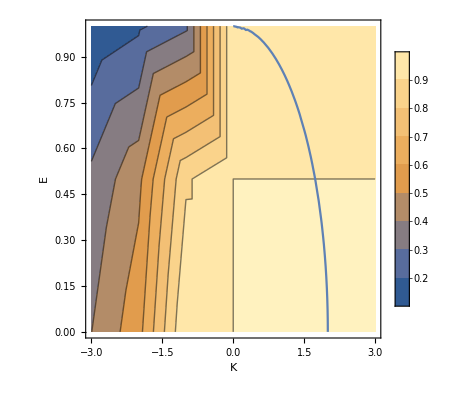

```mathematica
p1=ListContourPlot[data[[All,{1,2,4}]],FrameLabel->{Style["K",17,Italic],Style["E",Italic,17]},PlotLegends->Automatic,LabelStyle->13];
p2=ContourPlot[√(1-e1^2)-k/2==0,{k,-5,5},{e1,0,2}];
Show[{p1,p2}]
```

#### First

```mathematica
vmeans=Chop[data[[All,3]]];
sps=data[[All,4]];
sms=data[[All,5]];
temp=Table[
condSync=sms[[i]]>0.5&&vmeans[[i]]<0.01;
condPinned=sps[[i]]>0.95&&sms[[i]]<0.5&&vmeans[[i]]<0.01;
condFlipped=sps[[i]]<0.99&&vmeans[[i]]<0.01;
condUnsteady=vmeans[[i]]>0.01;
Which[condPinned,"pinned",condSync,"sync",condFlipped,"flipped",condUnsteady,"unsteady"],
{i,1,Length[sms]}
];
temp;
```

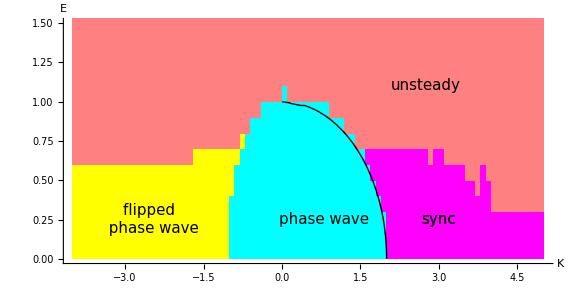

figures/bif-diagram-E-non-zero.png

```mathematica
Clear[colmap];
colmap[x1_]:=Which[x1=="pinned",Cyan,x1=="sync",Magenta,x1=="flipped",Yellow,x1=="unsteady",Pink,True,Cyan];
SetAttributes[colmap,Listable];
alldata={data[[All,1]],data[[All,2]],temp//colmap}ᵀ;
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->0.5,Axes->True,PlotRange->{0,1.5},LabelStyle->15,AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
Epilog->{Text[Style["unsteady",15],{2.75,1.1}],Text[Style["sync",15],{3,0.25}],Text[Style["sync",15],{3,0.25}],
Text[Style["phase wave",15],{0.8,0.25}],Text[Style["flipped \n phase wave",15],{-2.5,0.25}]
},ImageSize->Large];
p2=ContourPlot[√(1-e1^2)-k/2==0,{k,-5,5},{e1,0,1.3},ContourStyle->{Thick,Black}];
pc=Show[{p1,p2}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-non-zero.png",pc]
```

### Finer grain

```mathematica
run1[k1_,e_,T_,n_]:=Module[{J,K,dt,k,b,Ex,Eθ,b1,b2,t,NT,pin,z00,z0,znew,Wp,Wm,Wp1,Wm1,xs,x,theta,thetas,vmean,Sp,Sm,cutoff},

{dt}={0.5}; 
{J,k,b}={k1,k1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
{xs,thetas}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp1,Wm1}=findWs[znew];
{x,theta}=znew;AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
AppendTo[xs,x];AppendTo[thetas,theta];
];

cutoff=Round[0.9Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
vmean=findVmean[xs,thetas,dt];
Return[{vmean,Sp,Sm}]
]
```

```mathematica
data=Flatten[ParallelTable[{k,e,run1[k,e,150,200]}//Flatten,{k,-3,3,0.025},{e,0,1.2,0.025}],1];
data={data[[All,1]],data[[All,2]],data[[All,3]]/Max[data[[All,3]]],data[[All,4]],data[[All,5]]}ᵀ;
SetDirectory[NotebookDirectory[]];
Export["data/bif-diagram-e-non-zero.csv",data];
```

```mathematica
vmeans=Chop[data[[All,3]]];
sps=data[[All,4]];
sms=data[[All,5]];
temp=Table[
condSync=sms[[i]]>0.5&&vmeans[[i]]<0.01;
condPinned=sps[[i]]>0.95&&sms[[i]]<0.5&&vmeans[[i]]<0.01;
condFlipped=sps[[i]]<0.99&&vmeans[[i]]<0.01;
condUnsteady=vmeans[[i]]>0.01;
Which[condPinned,"pinned",condSync,"sync",condFlipped,"flipped",condUnsteady,"unsteady"],
{i,1,Length[sms]}
];
Clear[colmap];
colmap[x1_]:=Which[x1=="pinned",Cyan,x1=="sync",Magenta,x1=="flipped",Yellow,x1=="unsteady",Pink,True,Cyan];
SetAttributes[colmap,Listable];
alldata={data[[All,1]],data[[All,2]],temp//colmap}ᵀ;
```

#### Load data

```mathematica
data1=Import["data/bif-diagram-e-non-zero.csv"];
vmeans=Chop[data[[All,3]]];
sps=data[[All,4]];
sms=data[[All,5]];
temp=Table[
condSync=sms[[i]]>0.5&&vmeans[[i]]<0.01;
condPinned=sps[[i]]>0.95&&sms[[i]]<0.5&&vmeans[[i]]<0.01;
condFlipped=sps[[i]]<0.99&&vmeans[[i]]<0.01;
condUnsteady=vmeans[[i]]>0.01;
Which[condPinned,"pinned",condSync,"sync",condFlipped,"flipped",condUnsteady,"unsteady"],
{i,1,Length[sms]}
];
Clear[colmap];
colmap[x1_]:=Which[x1=="pinned",Cyan,x1=="sync",Magenta,x1=="flipped",Yellow,x1=="unsteady",Pink,True,Cyan];
SetAttributes[colmap,Listable];
alldata={data[[All,1]],data[[All,2]],temp//colmap}ᵀ;
```

#### Plot

```mathematica
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->0.5,Axes->True,PlotRange->{0,1.21},LabelStyle->15,AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
Epilog->{
Text[Style["sync",15],{3,0.4}],
Text[Style["phase wave",15],{0.8,0.4}],
Text[Style["split \n phase wave",15],{-2.0,0.25}],
Text[Style["bursty async",15],{-1.8,0.99}],
Rotate[Text[Style["hysteresis",13],{0.8,0.75}],-01 Degree],
Text[Style["quasi \n periodicity",14],{1.6,0.95}],
Text[Style["chaos",15],{1.05,1.15}],
Text[Style["periodic (flying saucers)",15],{2.85,1.2}]
},ImageSize->Large];
p2=ContourPlot[{√(1-e1^2)-k/2==0,√(1-e1^2)+k==0},{k,-5,5},{e1,0,1.3},ContourStyle->{{Thick,Black},{Thick,Black}}];
pc=Show[{p1,p2}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-non-zero.png",pc]
```

-Graphics-

figures/bif-diagram-E-non-zero.png

```mathematica
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->0.5,Axes->True,PlotRange->{0,1.18},LabelStyle->15,AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
Epilog->{
Text[Style["sync",15],{3,0.4}],
Text[Style["phase wave",15],{0.8,0.4}],
Text[Style["split \n phase wave",15],{-2.0,0.25}],
Text[Style["bursty async",15],{-1.8,0.99}],
Text[Style["Unsteady",15],{2.2,0.99}]
},ImageSize->Large];
p2=ContourPlot[{√(1-e1^2)-k/2==0,√(1-e1^2)+k==0},{k,-5,5},{e1,0,1.3},ContourStyle->{{Thick,Black},{Thick,Black}}];
pc=Show[{p1,p2}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-non-zero.png",pc]
```

-Graphics-

figures/bif-diagram-E-non-zero.png

### Finer grain: N = 200

```mathematica
run1[k1_,e_,T_,n_]:=Module[{J,K,dt,k,b,Ex,Eθ,b1,b2,t,NT,pin,z00,z0,znew,Wp,Wm,Wp1,Wm1,xs,x,theta,thetas,vmean,Sp,Sm,cutoff},

{dt}={0.5}; 
{J,k,b}={k1,k1,1};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
{xs,thetas}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp1,Wm1}=findWs[znew];
{x,theta}=znew;AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
AppendTo[xs,x];AppendTo[thetas,theta];
];

cutoff=Round[0.9Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
vmean=findVmean[xs,thetas];
Return[{vmean,Sp,Sm}]
]
```

```mathematica
data=Flatten[ParallelTable[{k,e,run1[k,e,150,200]}//Flatten,{k,-3,3,0.025},{e,0,1.2,0.025}],1];
data={data[[All,1]],data[[All,2]],data[[All,3]]/Max[data[[All,3]]],data[[All,4]],data[[All,5]]}ᵀ;
```

```mathematica
vmeans=Chop[data[[All,3]]];
sps=data[[All,4]];
sms=data[[All,5]];
temp=Table[
condSync=sms[[i]]>0.5&&vmeans[[i]]<0.01;
condPinned=sps[[i]]>0.95&&sms[[i]]<0.5&&vmeans[[i]]<0.01;
condFlipped=sps[[i]]<0.99&&vmeans[[i]]<0.01;
condUnsteady=vmeans[[i]]>0.01;
Which[condPinned,"pinned",condSync,"sync",condFlipped,"flipped",condUnsteady,"unsteady"],
{i,1,Length[sms]}
];
temp;
```

```mathematica
Clear[colmap];
colmap[x1_]:=Which[x1=="pinned",Cyan,x1=="sync",Magenta,x1=="flipped",Yellow,x1=="unsteady",Pink,True,Cyan];
SetAttributes[colmap,Listable];
alldata={data[[All,1]],data[[All,2]],temp//colmap}ᵀ;
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->0.5,Axes->True,PlotRange->{0,1.5},LabelStyle->15,AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
Epilog->{
Text[Style["unsteady",15],{2.75,1.0}],
Text[Style["sync",15],{3,0.4}],
Text[Style["phase wave",15],{0.8,0.4}],
Text[Style["flipped \n phase wave",15],{-2.0,0.25}]
},ImageSize->Large];
p2=ContourPlot[{√(1-e1^2)-k/2==0,√(1-e1^2)+k==0},{k,-5,5},{e1,0,1.3},ContourStyle->{{Thick,Black},{Thick,Black}}];
pc=Show[{p1,p2}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-non-zero.png",pc]
```

-Graphics-

figures/bif-diagram-E-non-zero.png

## E = 0 limits -- pictures

### Warm up

```mathematica
(*Preamble*)
{dt,n,T}={0.1,200,400}; 
{J,k}={-10,-10};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
results=plotResults[znew,pin]
```

```mathematica
size=25;
```

### Pinned state

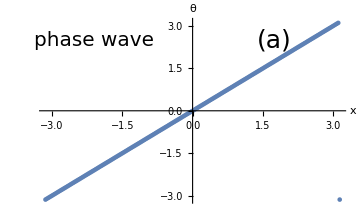

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={1,1};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p1=ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["phase wave",20],{-2.1,2.5}],Text[Style["(a)",25],{1.75,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

### Sync state

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={2,2};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;
```

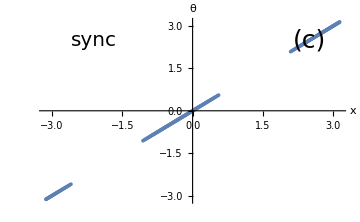

```mathematica
{x,θ}=znew;
p2= ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(c)",25],{2.5,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

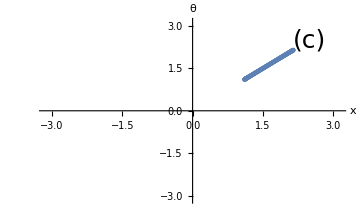

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={3,3};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{-0.25π,-0.5π}],{i,1,2},{j,1,n}],Table[RandomReal[{0.5π,1.0π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p4= ListPlot[{Mod[x,2π]-1.2π,Mod[θ,2π]-1.2π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,LabelStyle->15,ImageSize->Medium,PlotRange->{{-π,π},{-π,π}},
Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(c)",25],{2.5,2.5}]}]
```

### Split phase wave

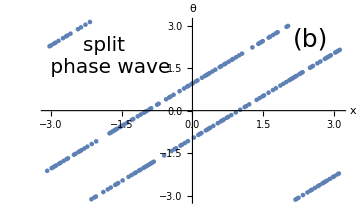

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={-2,-2};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p3= ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["split \n phase wave",20],{-1.8,1.9}],Text[Style["(b)",25],{2.5,2.5}]}]
```

### Plot together

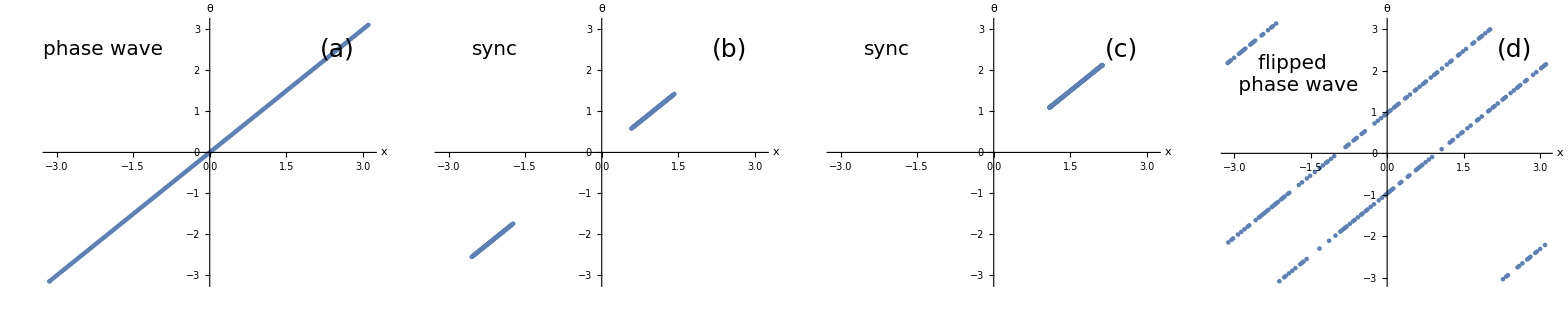

```mathematica
pAll=Grid[{{p1,p2,p4,p3}}]
SetDirectory[NotebookDirectory[]];
Export["figures/states-undriven.png",pAll];
```

```mathematica
pAll=Grid[{{p1,SpanFromLeft},{p3,p2}},Alignment->{Center,Center}]
SetDirectory[NotebookDirectory[]];
Export["figures/states-undriven.png",pAll];
```

-Graphics- | 
-Graphics- | -Graphics-

```mathematica
Clear[sm,k];
```

```mathematica
sol=Solve[sm==-2/k √((1-sm)/2) 1/(√(1-sm^2)) ,sm]//TableForm
```

sm→1/3 (-1+1/((-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3))+(-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3))
sm→-1/3-(1+ⅈ √3)/(6 (-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3))-1/6 (1-ⅈ √3) (-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3)
sm→-1/3-(1-ⅈ √3)/(6 (-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3))-1/6 (1+ⅈ √3) (-1+27/k^2+(3 √3 √(27-2 k^2))/k^2)^(1/3)

```mathematica
temp=sm-(-2/k √((1-sm)/2) 1/(√(1-sm^2)) );
FullSimplify[temp]
```

sm+(√2)/(k √(1+sm))

```mathematica
Numerator[Together[Numerator[temp]]]
```

√2 √(1-sm)+k sm √(1-sm^2)

```mathematica
sol=Solve[k^2 S^4-k^2 S^2-2S+2==0,S]//Flatten;
TableForm[sol]
```

S→1
S→1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)
S→-1/3-((1+ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1-ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)
S→-1/3-((1-ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1+ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)

```mathematica
sol
```

{{S→1},{S→1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)},{S→-1/3-((1+ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1-ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)},{S→-1/3-((1-ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1+ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)}}

```mathematica
sol
```

{S→1,S→1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2),S→-1/3-((1+ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1-ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2),S→-1/3-((1-ⅈ √3) k^2)/(6 (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))-((1+ⅈ √3) (27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/(6 k^2)}

```mathematica
FullSimplify[1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2),Assumptions->{k∈Reals}]
```

1/3 (-1+k^2/((27 k^4-k^6+3 √(81 k^8-6 k^10))^(1/3))+((27 k^4-k^6+3 √(81 k^8-6 k^10))^(1/3))/k^2)

```mathematica
(-1+k^2/((27 k^4-k^6+3 √(81 k^8-6 k^10))^(1/3))+((27 k^4-k^6+3 √(81 k^8-6 k^10))^(1/3))/k^2)/.k->K//TeXForm
```

\frac{K^2}{\sqrt[3]{-K^6+27 K^4+3 \sqrt{81 K^8-6 K^{10}}}}+\frac{\sqrt[3]{-K^6+27 K^4+3 \sqrt{81 K^8-6 K^{10}}}}{K^2}-1

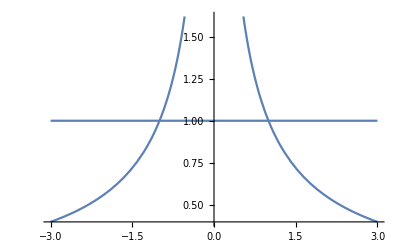

```mathematica
Plot[{S/.sol[[{1}]],S/.sol[[2]]}/.k->k1,{k1,-3,3}]
```

```mathematica
temp=sm+(2/k √((1-sm)/(2(1-sm)^2)));
```

```mathematica
t1=Numerator[Together[temp]]^2
```

(√2 √(-1/(-1+sm))+k sm)^2

```mathematica
Expand[t1^2]
```

4/(-1+sm)^2-(8 √2 k √(-1/(-1+sm)) sm)/(-1+sm)-(12 k^2 sm^2)/(-1+sm)+4 √2 k^3 √(-1/(-1+sm)) sm^3+k^4 sm^4

### S(K)

#### Make data

```mathematica
data=ParallelTable[
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.5,200,200}; 
{J,k}={K,K};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5 Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
{K,Sp,Sm},
{K,-5,5,0.1}
];
```

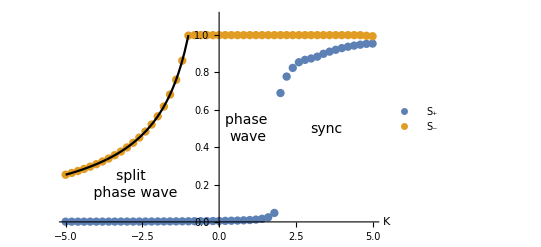

figures/order-pars-undriven.png

```mathematica
p1b=ListPlot[{data[[All,{1,2}]][[;;;;2]],data[[All,{1,3}]][[;;;;2]]},AxesLabel->{Style["K",22,Italic]},PlotLegends->{Style["S_+",19],Style["S_-",19]},LabelStyle->16,PlotRange->{0,1.1},PlotStyle->{PointSize[0.015]},Epilog->{Dashed,(*Line[{{-1,0},{-1,1}}],Line[{{2,0},{2,1}}],*)Text[Style["sync",14],{3.5,0.5}],Text[Style["phase \nwave",14],{0.95,0.5}],Text[Style["split \n phase wave",14],{-2.8,0.2}]}];
p2b=Plot[1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2),{k,-5,0},PlotRange->{0,1},PlotStyle->Black];
pAll3=Show[{p1b,p2b}]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-undriven.png",pAll3]
```

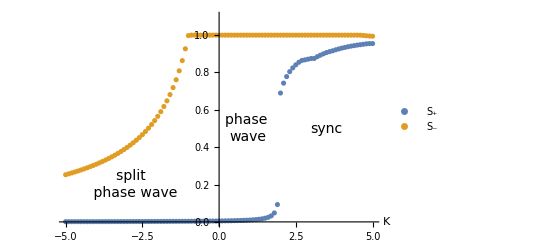

```mathematica
Show[{p1b,p2b}]
```

```mathematica
1/3 (-1+k^2/((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))+((27 k^4-k^6+3 √3 √(27 k^8-2 k^10))^(1/3))/k^2)/.k->-1//N
```

1.

```mathematica
\begin{equation}
K^2 S_-^3+K^2 S_-^2-2=0
\end{equation}
```

## E > 0 J = k -- pictures

$Aborted

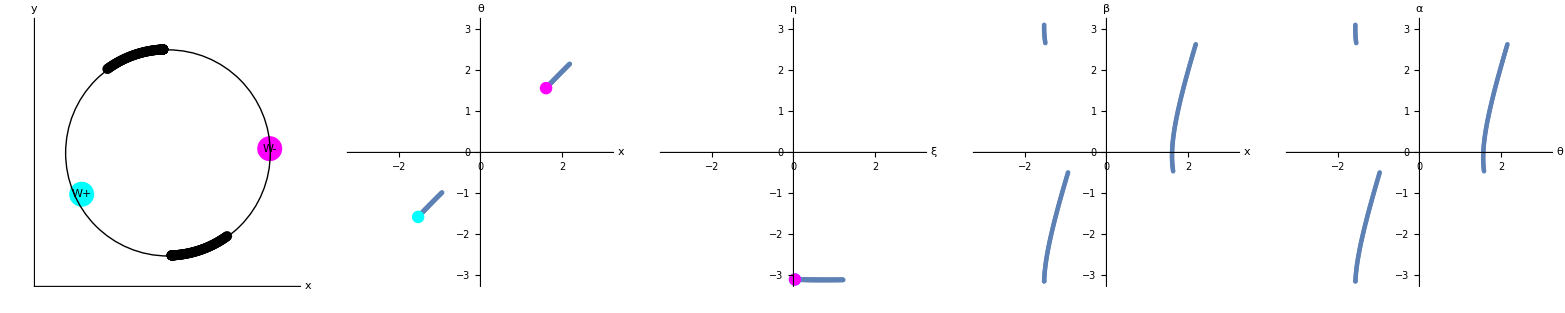

```mathematica
(*Preamble*)
{dt,n,T}={0.1,200,400}; 
{J,k}={3,3};
{e,b}={0.7,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]
results=plotResults[znew,pin]
```

```mathematica
size=25;
```

### Pinned state

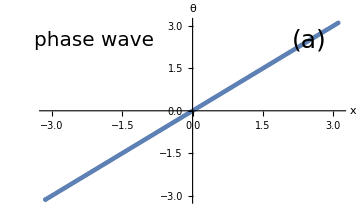

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={1,1};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p1=ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["phase wave",20],{-2.1,2.5}],Text[Style["(a)",25],{2.5,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

### Sync state

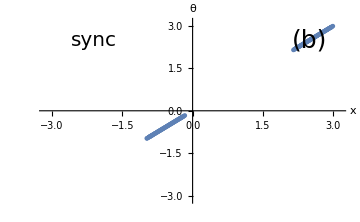

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,200}; 
{J,k}={3,3};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p2= ListPlot[{Mod[x,2π]-1.5π,Mod[θ,2π]-1.5π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(b)",25],{2.5,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

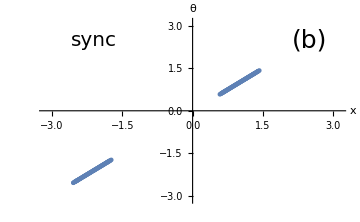

```mathematica
{x,θ}=z1;
p2= ListPlot[{Mod[x,2π]-1.5π,Mod[θ,2π]-1.5π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(b)",25],{2.5,2.5}]},PlotRange->{{-π,π},{-π,π}}]
```

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={3,3};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{-0.25π,-0.5π}],{i,1,2},{j,1,n}],Table[RandomReal[{0.5π,1.0π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p4= ListPlot[{Mod[x,2π]-1.2π,Mod[θ,2π]-1.2π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,LabelStyle->15,ImageSize->Medium,PlotRange->{{-π,π},{-π,π}},
Epilog->{Text[Style["sync",20],{-2.1,2.5}],Text[Style["(c)",25],{2.5,2.5}]}]
```

-Graphics-

### Flipped phase wave

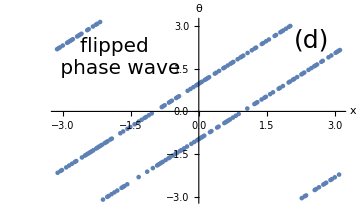

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,100}; 
{J,k}={-2,-2};
{e,b}={0,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
];
z1=znew;

{x,θ}=z1;
p3= ListPlot[{Mod[x,2π]-π,Mod[θ,2π]-π}ᵀ,AxesLabel->{Style["x",size,Italic],Style["θ",size,Italic]},LabelStyle->18,ImageSize->Medium,Epilog->{Text[Style["flipped \n phase wave",20],{-1.8,1.9}],Text[Style["(d)",25],{2.5,2.5}]}]
```

### Plot together

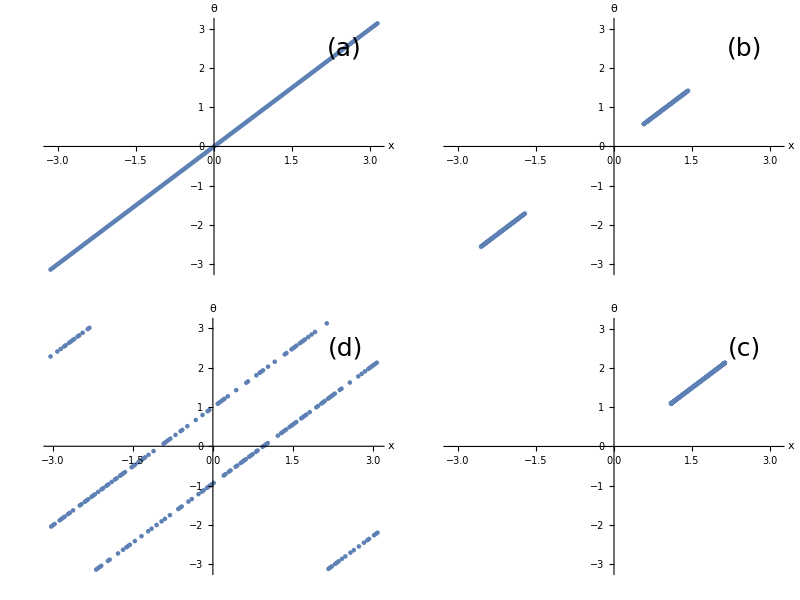

```mathematica
pAll=Grid[{{p1,p2},{p3,p4}}]
SetDirectory[NotebookDirectory[]];
Export["states-undriven.png",pAll];
```

```mathematica
pAll=Grid[{{p1,p2,p4,p3}}]
SetDirectory[NotebookDirectory[]];
Export["figures/states-undriven.png",pAll];
```

-Graphics-

### S(K)

#### Make data

```mathematica
data=ParallelTable[
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.5,200,200}; 
{J,k}={K,K};
{e,b}={0.75,1};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

cutoff=Round[0.5 Length[Wp]];
{Sp,Sm}={Abs[Wp[[cutoff;;-1]]]//Mean,Abs[Wm[[cutoff;;-1]]]//Mean};
If[Sp≤Sm,{Sp,Sm}={Sm,Sp}];
{K,Sp,Sm},
{K,-5,5,0.5}
];
```

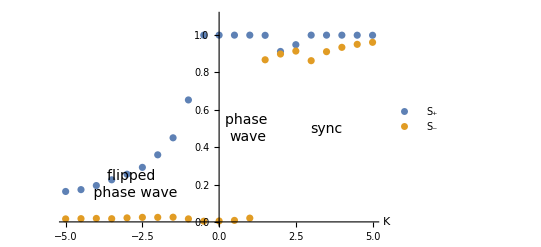

figures/order-pars-driven.png

```mathematica
p1c=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{Style["K",22,Italic]},PlotLegends->{Style["S_+",19],Style["S_-",19]},LabelStyle->16,PlotRange->{0,1.1},Epilog->{Dashed,(*Line[{{-1,0},{-1,1}}],Line[{{2,0},{2,1}}],*)Text[Style["sync",14],{3.5,0.5}],Text[Style["phase \nwave",14],{0.95,0.5}],Text[Style["flipped \n phase wave",14],{-2.8,0.2}]}]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-driven.png",p1b]
```

## Flying saucers

### Wave speed

#### Make data

```mathematica
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.5,200,500}; 
{J,k}={1,2};
{e,b}={1.5,0.75};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
]
```

#### Plot of order parameters

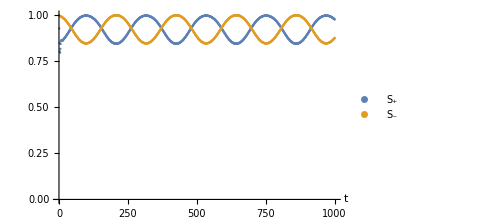
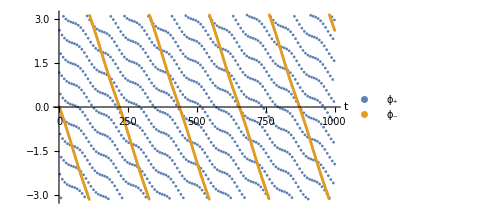
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{Wp//Abs,Wm//Abs},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1},ImageSize->Medium];
p2=ListPlot[{Wp//Arg,Wm//Arg},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},LabelStyle->15,PlotRange->All,ImageSize->Medium];
```

#### Measure wave speed S(E), Ω(E)

```mathematica
{ϕp,ϕm}={Wp//Arg,Wm//Arg};
ListPlot[{ϕp,ϕm}]
```

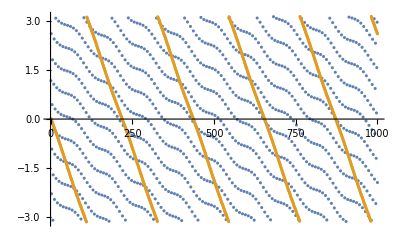

```mathematica
findWaveSpeed[ϕ_,dt_]:=Block[{vel,index,data},
index=Round[0.25*Length[ϕ]];
data=ϕ[[index;;-1]];
vel=Differences[data]/dt;
Return[Median[vel]]
]
```

```mathematica
findWaveSpeed[ϕp,dt]
```

2.76835

```mathematica
data=ParallelTable[
{dt,n,T}={0.1,500,200};
{J,k,b}={1,2,0.75};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{ϕp,ϕm}={Wps//Arg,Wms//Arg};
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{Ωp, Ωm}={findWaveSpeed[ϕp,dt]//Abs,findWaveSpeed[ϕm,dt]//Abs};
If[Ωp<Ωm,{Ωp,Ωm}={Ωm,Ωp}];
{e,Sp,Sm,Ωp,Ωm},
{e,0,0.8,0.025}
];
```

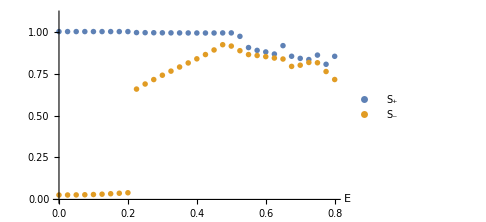

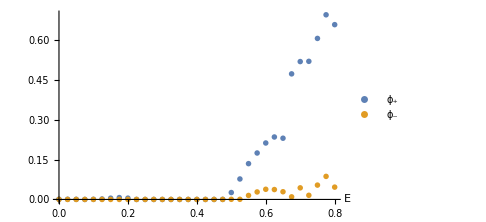

```mathematica
p3=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1},ImageSize->Medium]
p4=ListPlot[{data[[All,{1,4}]],data[[All,{1,5}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},PlotRange->All,LabelStyle->15,ImageSize->Medium]
```

#### Plot together

```mathematica
pAll=Grid[{{p1,p2},{p3,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/flying-saucers.png",pAll]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

figures/flying-saucers.png

## Sliding phase waves

#### Make data

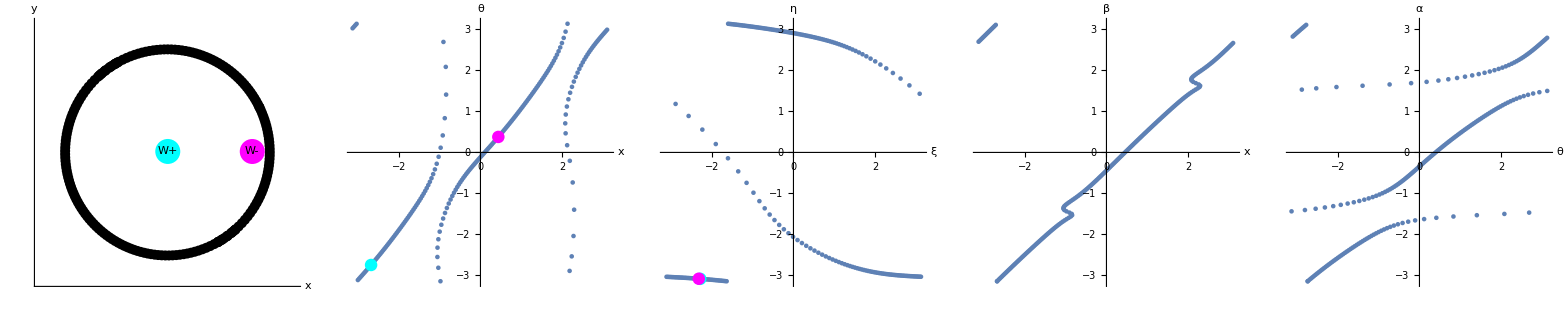

```mathematica
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.5,200,500}; 
{J,k}={1,-5};
{e,b}={0.9,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ;
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];
plotResults[znew,pin]
```

#### Make pics

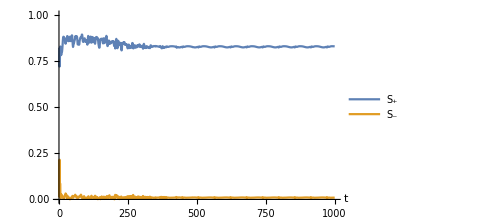
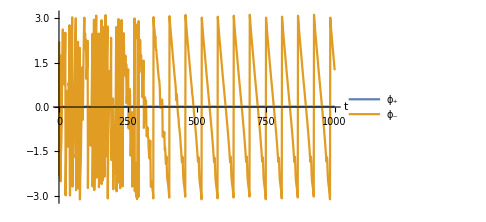
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{Wm//Abs,Wp//Abs},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1},ImageSize->Medium,Joined->True];
p2=ListPlot[{Wm//Arg,Wp//Arg},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},LabelStyle->15,PlotRange->All,ImageSize->Medium,Joined->True];
Grid[{{p1,p2}}]
```

#### Measure wave speed S(E), Ω(E)

```mathematica
data=ParallelTable[
{dt,n,T}={0.25,300,300};
{J,k,b}={1,-5,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{ϕp,ϕm}={Wps//Arg,Wms//Arg};
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{Ωp, Ωm}={findWaveSpeed[ϕp,dt]//Abs,findWaveSpeed[ϕm,dt]//Abs};
If[Ωp<Ωm,{Ωp,Ωm}={Ωm,Ωp}];
{e,Sp,Sm,Ωp,Ωm},
{e,0,4,0.025}
];
```

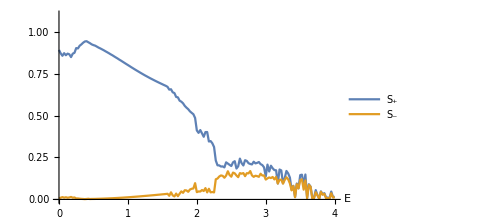

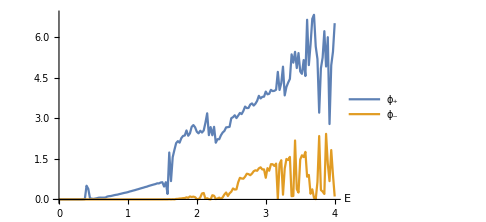

```mathematica
p3=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1},ImageSize->Medium,Joined->True]
p4=ListPlot[{data[[All,{1,4}]],data[[All,{1,5}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},PlotRange->All,LabelStyle->15,ImageSize->Medium,Joined->True]
```

#### Plot together

```mathematica
pAll=Grid[{{p1,p3},{p2,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/sliding-phase-wave.png",pAll]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

figures/sliding-phase-wave.png

## Messy phase waves

#### Make data

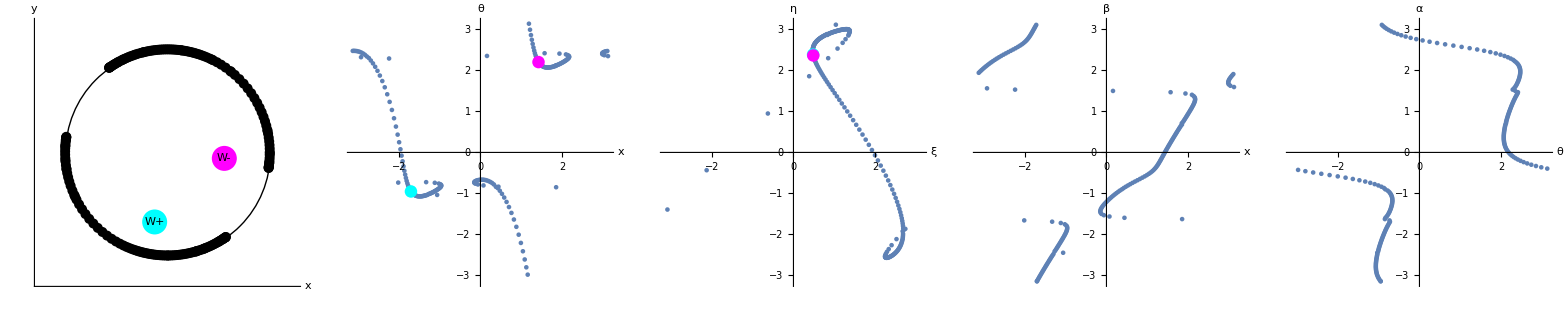

```mathematica
(*Preamble*)
SeedRandom[0];
{dt,n,T}={0.25,200,200}; 
{J,k}={1,2};
{e,b}={1.9,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ;
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];
plotResults[znew,pin]
```

#### Make pics

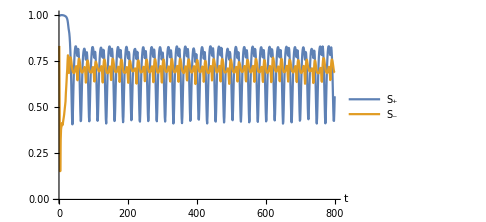
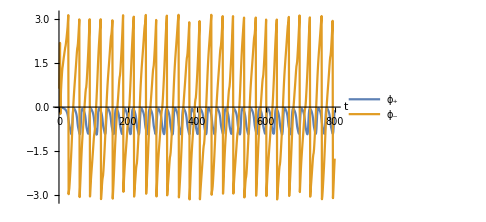
-Graphics- | -Graphics-

```mathematica
p1=ListPlot[{Wm//Abs,Wp//Abs},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1},ImageSize->Medium,Joined->True];
p2=ListPlot[{Wm//Arg,Wp//Arg},AxesLabel->{Style["t",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},LabelStyle->15,PlotRange->All,ImageSize->Medium,Joined->True];
Grid[{{p1,p2}}]
```

#### Measure wave speed S(E), Ω(E)

```mathematica
data=ParallelTable[
{dt,n,T}={0.25,300,300};
{J,k,b}={1,2,2};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{1.9π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{ϕp,ϕm}={Wps//Arg,Wms//Arg};
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{Ωp, Ωm}={findWaveSpeed[ϕp,dt]//Abs,findWaveSpeed[ϕm,dt]//Abs};
If[Ωp<Ωm,{Ωp,Ωm}={Ωm,Ωp}];
{e,Sp,Sm,Ωp,Ωm},
{e,0,3.5,0.025}
];
```

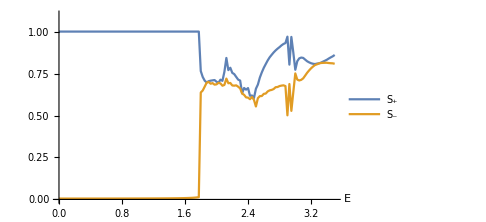

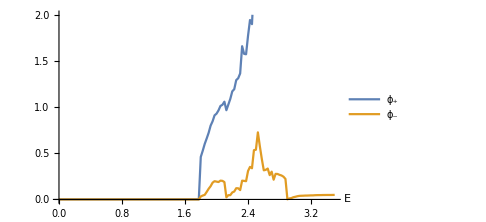

```mathematica
p3=ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1},ImageSize->Medium,Joined->True]
p4=ListPlot[{data[[All,{1,4}]],data[[All,{1,5}]]},AxesLabel->{Style["E",18,Italic],Style["",18,Italic]},PlotLegends->{"ϕ_+","ϕ_-"},PlotRange->{0,2},LabelStyle->15,ImageSize->Medium,Joined->True]
```

#### Plot together

```mathematica
pAll=Grid[{{p1,p3},{p2,p4}}]
SetDirectory[NotebookDirectory[]];
Export["figures/messy-phase-wave.png",pAll]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

figures/messy-phase-wave.png

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[Mod[{x+θ,x-θ}ᵀ,2π],PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];

findWaveSpeed[ϕ_,dt_]:=Block[{vel,index,data},
index=Round[0.25*Length[ϕ]];
data=ϕ[[index;;-1]];
vel=Differences[data]/dt;
Return[Median[vel]]
];

findVmean[xs_,thetas_]:=Module[{vx,vtheta,tcutoff,vxMean,vthetaMean,vMean},
{vx,vtheta}={{},{}};
tcutoff=Round[0.9Dimensions[xs][[2]]];
vxMean=Table[Mean[Differences[xs[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vthetaMean=Table[Mean[Differences[thetas[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vMean=√(vxMean^2+vthetaMean^2);
Return[vMean]
]
```